# Micro-Mobility Model

```mathematica
Clear["Global`*"]
```

## Congestion Fee Basic Model

### Basic Model

```mathematica
s[q_]:=(1-q/A)^2
d[p_,q_]:=m*(1-p-s[q])
Π[p_,q_]:=p*q -γ*q
Α[p_,q_]:=p*q -(p+α)*(q-d[p,q])-γ*q
```

```mathematica
Simplify[D[Π[p,q], q]]
Simplify[D[Α[p,q], q]]
```

p-γ

(2 A m (p+α)-2 m q (p+α)-A^2 (α+γ))/A^2

```mathematica
Simplify[Solve[s[q]==1-p,q]]
Simplify[Solve[q==d[p,q],q]]
Simplify[Solve[D[Α[p,q], q]==0,q]]
```

{{q→A-A √(1-p)},{q→A (1+√(1-p))}}

{{q→-(A (A-2 m+√(A^2-4 A m-4 m^2 (-1+p))))/(2 m)},{q→(A (-A+2 m+√(A^2-4 A m-4 m^2 (-1+p))))/(2 m)}}

{{q→A-(A^2 (α+γ))/(2 m (p+α))}}

```mathematica
Reduce[A-A √(1-p)>0&&0<p<1]
Reduce[A (1+√(1-p))>0&&0<p<1]
```

A>0&&0<p<1

A>0&&0<p<1

```mathematica
(* Sanity check on p and q *)
Simplify[Solve[D[Α[p,q], q]==0,q]]
Simplify[Solve[D[Α[p,q], p]==0,p]]
```

{{q→A-(A^2 (α+γ))/(2 m (p+α))}}

{{p→-(-2 A q+q^2+A^2 α)/(2 A^2)}}

```mathematica
(* Simplify[Solve[D[Α[p,q], q]==0&&D[Α[p,q], p]==0,{p,q}]] *) (* Complicated *)
```

```mathematica
(* Value of profit function *)
Simplify[Α[p,A-(A^2 (α+γ))/(2 m (p+α))]]
Simplify[Reduce[Α[p,A-(A^2 (α+γ))/(2 m (p+α))]≥0&&0<p<1&&0<α<1&&0<γ<p&&m>0&&A>0,A]]
```

-m (-1+p) (p+α)-A (α+γ)+(A^2 (α+γ)^2)/(4 m (p+α))

0<α<1&&0<p<1&&0<γ<p&&m>0&&(0<A≤-2 √((m^2 p (p+α)^2)/(α+γ)^2)+(2 m (p+α))/(α+γ)||A≥2 (√((m^2 p (p+α)^2)/(α+γ)^2)+(m (p+α))/(α+γ)))

### Analysis on Feasibility

```mathematica
(* When q1 feasible *)
Simplify[Reduce[A-A √(1-p)<(A (-A+2 m+√(A^2-4 A m-4 m^2 (-1+p))))/(2 m)&&0<p<1&&m>0&&A>m]]
```

m>0&&m<A<2 m&&0<p≤(A-2 m)^2/(4 m^2)

```mathematica
(* q2 is always greater than ql *)
Simplify[Reduce[A-A √(1-p)<A-(A^2 (α+γ))/(2 m (p+α))&&0<p<1&&0<α<1&&0<γ<p&&m>0&&A>0&&m<A<2 m&&0<p≤(A-2 m)^2/(4 m^2)]]
Simplify[Reduce[A (1+√(1-p))>A-(A^2 (α+γ))/(2 m (p+α))&&0<p<1&&0<α<1&&0<γ<p&&m>0&&A>0&&m<A<2 m&&0<p≤(A-2 m)^2/(4 m^2)]]
```

m>0&&m<A<2 m&&0<p≤(A-2 m)^2/(4 m^2)&&0<α<1&&0<γ<p

m>0&&m<A<2 m&&0<p≤(A-2 m)^2/(4 m^2)&&0<α<1&&0<γ<p

```mathematica
(* ql falls in the second range, so q2 is feasible *)
Simplify[Reduce[d[p,A-A √(1-p)]≤ A-A √(1-p)&&0<p<1&&0<α<1&&0<γ<p&&m>0&&A>0&&m<A<2 m&&0<p≤(A-2 m)^2/(4 m^2)]]
```

0<α<1&&m>0&&m<A<2 m&&0<p≤(A-2 m)^2/(4 m^2)&&0<γ<p

```mathematica
(* When q1 < ql infeasible *)
Simplify[Reduce[A-A √(1-p)>(A (-A+2 m+√(A^2-4 A m-4 m^2 (-1+p))))/(2 m)&&0<p<1&&m>0&&A>m]]
```

m>0&&0<p&&((A==4 m&&p<(A-2 m)^2/(4 m^2))||(A<4 m&&2 m<A&&p≤(A-2 m)^2/(4 m^2))||(A>4 m&&p<1))

```mathematica
(* ql falls in the second range *)
Simplify[Reduce[d[p,A-A √(1-p)]≤ A-A √(1-p)&&0<p<1&&0<α<1&&0<γ<p&&m>0&&A>0&&2m≤A]]
```

0<α<1&&0<γ<1&&γ<p<1&&m>0&&A≥2 m

```mathematica
(* q2 > ql always feasible *)
Simplify[Reduce[A-A √(1-p)<A-(A^2 (α+γ))/(2 m (p+α))&&0<p<1&&0<α&&0<γ&&m>0&&A>0,A]]
(* Case one *)
Simplify[Reduce[A-A √(1-p)<A-(A^2 (α+γ))/(2 m (p+α))&&0<p<1&&0<α<1&&0<γ<p&&m>0&&A>0&&2 m<A<4m&&p≤(A-2 m)^2/(4 m^2)]]
(* Simplify[Reduce[A (1+√(1-p))≥A-(A^2 (α+γ))/(2 m (p+α))&&0<p<1&&0<α<1&&0<γ<p&&m>0&&A>0&&2m<A<4m&&p≤(A-2 m)^2/(4 m^2)]]*)
(* Case two *)
Simplify[Reduce[A-A √(1-p)<A-(A^2 (α+γ))/(2 m (p+α))&&0<p<1&&0<α<1&&0<γ<p&&m>0&&A>0&&A>4 m,A]]
(* Simplify[Reduce[A (1+√(1-p))≥A-(A^2 (α+γ))/(2 m (p+α))&&0<p<1&&0<α<1&&0<γ<p&&m>0&&A>0&&A>4m]]*)
```

α>0&&0<p<1&&γ>0&&m>0&&0<A<2 √(-(m^2 (-1+p) (p+α)^2)/(α+γ)^2)

m>0&&2 m<A<4 m&&0<p≤(A-2 m)^2/(4 m^2)&&0<α<2 (-(2 m^2 (-1+p) p)/(A^2+4 m^2 (-1+p))+√(-(A^2 m^2 (-1+p) p^2)/((A^2+4 m^2 (-1+p))^2)))&&γ>0&&2 √(-(m^2 (-1+p) (p+α)^2)/A^2)>α+γ

0<α<Root0.278Root[1+3 #1-24 #1^2+#1^3&,2]0.2780661432813855&&Root[3 α^2+(-2 α+α^2) #1+(-1+2 α) #1^2+#1^3&,2]<p<Root[3 α^2+(-2 α+α^2) #1+(-1+2 α) #1^2+#1^3&,3]&&γ>0&&√(-(-1+p) (p+α)^2)>2 (α+γ)&&m>0&&4 m<A<2 √(-(m^2 (-1+p) (p+α)^2)/(α+γ)^2)

### Plots

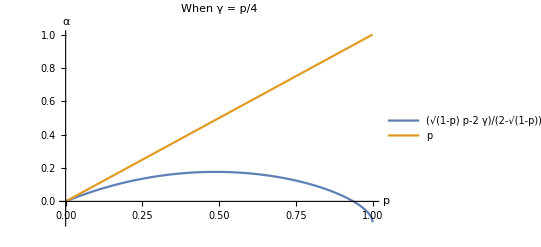

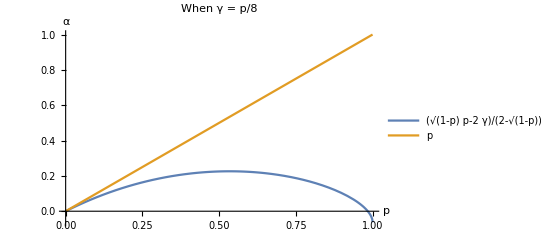

```mathematica
p1 = Plot[{(p*Sqrt[1-p]-p/4)/(2-Sqrt[1-p]), p},{p,0,1},AxesLabel->{p,α},PlotLegends-> {(p*Sqrt[1-p]-2γ)/(2-Sqrt[1-p]),p},PlotLabel->"When γ = p/4"]
p2 = Plot[{(p*Sqrt[1-p]-p/8)/(2-Sqrt[1-p]), p},{p,0,1},AxesLabel->{p,α},PlotLegends-> {(p*Sqrt[1-p]-2γ)/(2-Sqrt[1-p]),p},PlotLabel->"When γ = p/8"]
```

```mathematica
Manipulate[Plot[(2*(p+α)*Sqrt[1-p])/(α+γ),{α,0,1}],{p,0.001,1},{γ,0.001,p}]
```

(-√(1-p) p+γ)/(-2+√(1-p))>α&&0<p<1&&0<γ<p&&0<α<p

```mathematica
(* (2*(p+α)*Sqrt[1-p])/(α+γ) ≥ 4 *)
Simplify[Reduce[(2*(p+1)*Sqrt[1-p])/(1+γ)≥ 4&&0<p<1&&0<γ<p]]
```

False

### Without congestion fee

```mathematica
s[q_]:=(1-q/A)^2
d[p_,q_]:=m*(1-p-s[q])
Π[p_,q_]:=p*q -γ*q
Α[p_,q_]:=p*d[p,q]-γ*q
Simplify[D[Π[p,q], q]]
Simplify[D[Α[p,q], q]]
```

p-γ

(2 m p (A-q))/A^2-γ

```mathematica
Simplify[Solve[Simplify[D[Α[p,q], q]]==0,q]]
```

{{q→A-(A^2 γ)/(2 m p)}}

```mathematica
Reduce[A-(A^2 γ)/(2 m p)≥A-A √(1-p)&&0<p<1&&0<γ<1&&m>0&&A>m]
```

0<p<1&&0<γ<√(4 p^2-4 p^3)&&A>0&&1/2 √(-(A^2 γ^2)/((-1+p) p^2))≤m<A

## Price Endogenous

### Basic model

```mathematica
Clear["Global`*"]
s[q_]:=(1-q/A)^2
d[p_,q_]:=m*(1-p-s[q])
Π[p_,q_]:=p*q -γ*q
Α[p_,q_]:=p*q -(p+α)*(q-d[p,q])-γ*q
```

```mathematica
Simplify[D[Π[p,q],p]]
Simplify[D[Π[p,q],q]]
```

q

p-γ

```mathematica
Simplify[D[Α[p,q],p]]
Simplify[D[Α[p,q],q]]
```

-(m (-2 A q+q^2+A^2 (2 p+α)))/A^2

(2 A m (p+α)-2 m q (p+α)-A^2 (α+γ))/A^2

```mathematica
Simplify[Α[p,A-(A^2 (α+γ))/(2 m (p+α))]]
Simplify[p*(A-(A^2 (α+γ))/(2 m (p+α))) -(p+α)*(A-(A^2 (α+γ))/(2 m (p+α))-d[p,A-(A^2 (α+γ))/(2 m (p+α))])-γ*(A-(A^2 (α+γ))/(2 m (p+α)))]
```

-m (-1+p) (p+α)-A (α+γ)+(A^2 (α+γ)^2)/(4 m (p+α))

-m (-1+p) (p+α)-A (α+γ)+(A^2 (α+γ)^2)/(4 m (p+α))

```mathematica
Simplify[Reduce[-m (-1+γ) (γ+α)-A (α+γ)+(A^2 (α+γ)^2)/(4 m (γ+α))>0&&0<α<1&&0<γ<1&&m>0&&A>0]]
```

m>0&&0<α&&0<γ&&α<1&&((γ<(A-2 m)^2/(4 m^2)&&((0<A&&A<2 m)||(A<4 m&&2 m<A)))||(A≥4 m&&γ<1))

### Range of price

```mathematica
Simplify[D[(2*p*Sqrt[1-p])/γ,p]]
Simplify[Solve[D[(2*p*Sqrt[1-p])/γ,p]==0,p]]
```

(2-3 p)/(√(1-p) γ)

{{p→2/3}}

```mathematica
(* K at candidate points *)
Simplify[(2*2/3*Sqrt[1-2/3])/γ]
Simplify[(2*1*Sqrt[1-1])/γ]
Simplify[(2*γ*Sqrt[1-γ])/γ]
```

4/(3 √3 γ)

0

2 √(1-γ)

```mathematica
(* Solve system of equations *)
(* Simplify[Reduce[p*Sqrt[1-p] + α*Sqrt[1-p]== (A*(α+γ))/(2m)&&0<p<1&&0<α<1&&0<γ<p&&m>0&&A>0,p]] *)
Manipulate[Plot[p*Sqrt[1-p] + α*Sqrt[1-p],{p,0,1}],{α,0,1}]
```

A>0&&((α>0&&p==Root[A^2 α^2-4 m^2 α^2+2 A^2 α γ+A^2 γ^2+(-8 m^2 α+4 m^2 α^2) #1+(-4 m^2+8 m^2 α) #1^2+4 m^2 #1^3&,2]&&((α+3 γ<2&&1/3<γ<2/3)||(α<1&&3 γ≤1&&γ>0))&&(3 √3 √((A^2 (α+γ)^2)/(1+α)^3)==4 m||(√(-A^2/(-1+γ))>2 m&&3 √3 √((A^2 (α+γ)^2)/(1+α)^3)<4 m)))||(p==Root[A^2 α^2-4 m^2 α^2+2 A^2 α γ+A^2 γ^2+(-8 m^2 α+4 m^2 α^2) #1+(-4 m^2+8 m^2 α) #1^2+4 m^2 #1^3&,3]&&((1+2 γ==√5&&((α<1&&√(-A^2/(-1+γ))<2 m&&α+3 γ≥2)||(α>0&&α+3 γ<2&&(√(-A^2/(-1+γ))≤2 m||3 √3 √((A^2 (α+γ)^2)/(1+α)^3)<4 m))))||(3 √3 √((A^2 (α+γ)^2)/(1+α)^3)<4 m&&((α+3 γ==2&&((1+2 γ<√5&&3 γ>1)||(3 γ<2&&1+2 γ>√5)))||(α>0&&((α<1&&3 γ≤1&&γ>0)||(α+3 γ<2&&((3 γ>1&&1+2 γ<√5)||(1+2 γ>√5&&3 γ<2)))))))||(α<1&&((√(-A^2/(-1+γ))<2 m&&((α+3 γ>2&&((1+2 γ>√5&&3 γ<2)||(3 γ>1&&1+2 γ<√5)))||(3 γ≥2&&γ<1&&α>0)))||(α>0&&√(-A^2/(-1+γ))≤2 m&&γ>0&&3 γ≤1)))||(α>0&&√(-A^2/(-1+γ))≤2 m&&α+3 γ<2&&((1+2 γ<√5&&3 γ>1)||(3 γ<2&&1+2 γ>√5))))))

```mathematica
(* LHS attain its maximum at (2-α)/3 *)
Simplify[D[p*Sqrt[1-p] + α*Sqrt[1-p],p]]
Simplify[Solve[D[p*Sqrt[1-p] + α*Sqrt[1-p],p]==0,p]]
Simplify[Reduce[((2-α)/3)*Sqrt[1-(2-α)/3] + α*Sqrt[1-(2-α)/3]> (A*(α+γ))/(2m)&&0<α<1&&0<γ<1&&m>0&&A>0,A]]
```

(2-3 p-α)/(2 √(1-p))

{{p→(2-α)/3}}

0<γ<1&&0<α<1&&m>0&&A>0&&4 √3 √((m^2 (1+α)^3)/(α+γ)^2)>9 A

```mathematica
(* Plot the feasible upper bound on A *)
Manipulate[Plot[(4 √3)/9 √((1+α)^3/(α+γ)^2),{α,0,1}],{γ,0.0001,1}]
```

```mathematica
(* LHS at γ *)
Simplify[Reduce[γ*Sqrt[1-γ] + α*Sqrt[1-γ]> (A*(α+γ))/(2m)&&0<α<1&&0<γ<1&&m>0&&A>0]]
```

m>0&&0<A<2 m&&γ>0&&A^2/m^2+4 γ<4&&0<α<1

### pl, pr

```mathematica
A = 200; m = 100;γ = 0.1;
α = 0.001;
Solve[p*Sqrt[1-p] + α*Sqrt[1-p]== (A*(α+γ))/(2m),p]
α = 0.01;
Solve[p*Sqrt[1-p] + α*Sqrt[1-p]== (A*(α+γ))/(2m),p]
α = 0.02;
Solve[p*Sqrt[1-p] + α*Sqrt[1-p]== (A*(α+γ))/(2m),p]
α = 0.03;
Solve[p*Sqrt[1-p] + α*Sqrt[1-p]== (A*(α+γ))/(2m),p]
α = 0.05;
Solve[p*Sqrt[1-p] + α*Sqrt[1-p]== (A*(α+γ))/(2m),p]
α = 0.1;
Solve[p*Sqrt[1-p] + α*Sqrt[1-p]== (A*(α+γ))/(2m),p]
α = 0.2;
Solve[p*Sqrt[1-p] + α*Sqrt[1-p]== (A*(α+γ))/(2m),p]
α = 0.3;
Solve[p*Sqrt[1-p] + α*Sqrt[1-p]== (A*(α+γ))/(2m),p]
```

{{p→0.105809},{p→0.989605}}

{{p→0.106362},{p→0.987848}}

{{p→0.106985},{p→0.985765}}

{{p→0.107615},{p→0.983549}}

{{p→0.108902},{p→0.97874}}

{{p→0.112271},{p→0.964715}}

{{p→0.119757},{p→0.929448}}

{{p→0.128468},{p→0.88631}}

```mathematica
Manipulate[Plot[p*Sqrt[1-p] + α*Sqrt[1-p]- (A*(α+γ))/(2m),{p,0,1}],{α,0,1}]
```

### Concavity and Feasibility

```mathematica
Simplify[D[Α[p,A-(A^2 (α+γ))/(2 m (p+α))],p]]
Simplify[D[D[Α[p,A-(A^2 (α+γ))/(2 m (p+α))],p],p]]
```

-m (-1+2 p+α)-(A^2 (α+γ)^2)/(4 m (p+α)^2)

(-4 m^2 (p+α)^3+A^2 (α+γ)^2)/(2 m (p+α)^3)

```mathematica
(* 1st derivative at 0 & 1, α *)
Simplify[Reduce[-m (-1+α)-(A^2 (α+γ)^2)/(4 m (α)^2)<0&&0<α<1&&0<γ<1&&m>0&&A>0,A]]
Simplify[Reduce[-m (-1+2+α)-(A^2 (α+γ)^2)/(4 m (1+α)^2)<0&&0<α<1&&0<γ<1&&m>0&&A>0]]
Simplify[Reduce[-m (-1+2 α+α)-(A^2 (α+γ)^2)/(4 m (α+α)^2)>0&&0<α<1&&0<γ<1&&m>0&&A>0,A]]
```

0<γ<1&&0<α<1&&m>0&&A>2 √(-(m^2 (-1+α) α^2)/(α+γ)^2)

0<γ<1&&0<α<1&&m>0&&A>0

0<γ<1&&0<α<1/3&&m>0&&0<A<4 √(-(m^2 α^2 (-1+3 α))/(α+γ)^2)

```mathematica
(* The 2nd derivative is decreasing in p *)
Simplify[D[(-4 m^2 (p+α)^3+A^2 (α+γ)^2)/(2 m (p+α)^3),p]]
```

-(3 A^2 (α+γ)^2)/(2 m (p+α)^4)

```mathematica
(* 2nd derivative at p = 0, α, γ, 1 *)
Simplify[Reduce[(-4 m^2 (0+α)^3+A^2 (α+γ)^2)/(2 m (0+α)^3)<0&&0<α<1&&0<γ<1&&m>0&&A>0,A]]
Simplify[Reduce[(-4 m^2 (α+α)^3+A^2 (α+γ)^2)/(2 m (α+α)^3)<0&&0<α<1&&0<γ<1&&m>0&&A>0,A]]
Simplify[Reduce[(-4 m^2 (γ+α)^3+A^2 (α+γ)^2)/(2 m (γ+α)^3)<0&&0<α<1&&0<γ<1&&m>0&&A>0,A]]
Simplify[Reduce[(-4 m^2 (1+α)^3+A^2 (α+γ)^2)/(2 m (1+α)^3)<0&&0<α<1&&0<γ<1&&m>0&&A>0,A]]
```

0<γ<1&&0<α<1&&m>0&&0<A<2 √((m^2 α^3)/(α+γ)^2)

0<γ<1&&0<α<1&&m>0&&0<A<4 √2 √((m^2 α^3)/(α+γ)^2)

0<γ<1&&0<α<1&&m>0&&0<A<2 √(m^2 (α+γ))

0<γ<1&&0<α<1&&m>0&&0<A<2 √((m^2 (1+α)^3)/(α+γ)^2)

```mathematica
Simplify[Reduce[A<2 √(m^2 (α+γ))&&0<α<1&&0<γ<1&&m>0&&A>0,α]]
```

m>0&&((A^2/m^2<4 (α+γ)&&α<1&&((γ<1&&((A==2 m&&0<γ)||(A<2 √2 √(m^2)&&A^2/m^2<4+4 γ&&2 m<A)))||(A<2 m&&A^2/m^2≥4 γ&&A>0&&γ>0)))||(A>0&&A<2 m&&0<α<1&&A^2/m^2<4 γ&&γ<1))

```mathematica
(* Compare two threshold *)
Simplify[Reduce[4 √2 √((m^2 α^3)/(α+γ)^2)<4 √(-(m^2 α^2 (-1+3 α))/(α+γ)^2)&&0<α<1&&0<γ<1&&m>0]]
Simplify[Reduce[4 √2 √((m^2 α^3)/(α+γ)^2)>4 √(-(m^2 α^2 (-1+3 α))/(α+γ)^2)&&0<α<1&&0<γ<1&&m>0]]
```

0<γ<1&&0<α<1/5&&m>0

0<γ<1&&1/5<α≤1/3&&m>0

```mathematica
(* Compare with m *)
Simplify[Reduce[4 √2 √((m^2 α^3)/(α+γ)^2)>m&&0<α<1/5&&0<γ<1&&m>1]]
```

γ>0&&5+25 γ<4 √10&&Root[-γ^2-2 γ #1-#1^2+32 #1^3&,1]<α<1/5&&m>1

```mathematica
Manipulate[Plot[(32 α^3)/(α+γ)^2,{α,0,1}],{γ,0,1}]
```

```mathematica
Simplify[Reduce[4/(3 √3 γ)<2 √(α+γ)&&0<α<1&&0<γ<1,γ]]
Simplify[Solve[4/(3 √3 γ)==2 √(α+γ),α]]
```

0<α<1&&Root[-4+27 α #1^2+27 #1^3&,1]<γ<1

{{α→4/(27 γ^2)-γ}}

```mathematica
Simplify[D[4/(27 γ^2)-γ,γ]]
```

-1-8/(27 γ^3)

```mathematica
Simplify[Reduce[4/(3 √3 γ)<2 √(α+γ)&&0<α<1&&0<γ<α/5,γ]]
```

False

```mathematica
(* Compare Kalpha and Kp, but p is also a function of alpha... *)
Reduce[√(α+γ)<(p*Sqrt[1-p])/γ&&0<α<1&&0<γ<p&&0<p<1]
```

(0<γ<1/3&&((γ<p≤(1+γ)/2-1/2 √(1-2 γ-3 γ^2)&&0<α<(p^2-p^3-γ^3)/γ^2)||((1+γ)/2-1/2 √(1-2 γ-3 γ^2)<p≤(1+γ)/2+1/2 √(1-2 γ-3 γ^2)&&0<α<1)||((1+γ)/2+1/2 √(1-2 γ-3 γ^2)<p<Root[γ^3-#1^2+#1^3&,3]&&0<α<(p^2-p^3-γ^3)/γ^2)))||(γ==1/3&&((1/3<p<2/3&&0<α<9 (-1/27+p^2-p^3))||(p==2/3&&0<α<1)||(2/3<p<Root0.960Root[1-27 #1^2+27 #1^3&,3]0.9597950805239389&&0<α<9 (-1/27+p^2-p^3))))||(1/3<γ≤1/2&&γ<p<Root[γ^3-#1^2+#1^3&,3]&&0<α<(p^2-p^3-γ^3)/γ^2)||(1/2<γ<Root0.529Root[-4+27 #1^3&,1]0.5291336839893999&&Root[γ^3-#1^2+#1^3&,2]<p<Root[γ^3-#1^2+#1^3&,3]&&0<α<(p^2-p^3-γ^3)/γ^2)

```mathematica
(* Kalpha attain maximum at 2/3 *)
Simplify[D[(p*Sqrt[1-p])/γ,p]] 
(* Plug back to pi0's derivative, 2/3 is at the right hand side of p0 *)
Simplify[m-2 m 2/3-(A^2 γ^2)/(4 m (2/3)^2)]
Simplify[Reduce[-m/3-(9 A^2 γ^2)/(16 m)≤0&&0<γ<1&&m>0&&A>0]]
```

(2-3 p)/(2 √(1-p) γ)

-m/3-(9 A^2 γ^2)/(16 m)

m>0&&0<γ<1&&A>0

```mathematica
(* Maximum bound, 2/3 *)
Simplify[(2/3*Sqrt[1-2/3])/γ]
(* Minimum bound, 0 *)
Simplify[√(0+γ)]
(* Compare *)
Reduce[2/(3 √3 γ)≤ √γ&&0<γ<1]
```

2/(3 √3 γ)

√γ

Root0.529Root[-4+27 #1^3&,1]0.5291336839893999≤γ<1

```mathematica
Simplify[Solve[2/(3 √3 γ)== √γ,γ]]
```

{{γ→2^(2/3)/3}}

```mathematica
Simplify[Solve[√(α+γ) == (p*Sqrt[1-p])/γ,p]]
```

{{p→1/6 (2+(2 2^(1/3))/((2-27 α γ^2-27 γ^3+√(-4+(-2+27 α γ^2+27 γ^3)^2))^(1/3))+2^(2/3) (2-27 α γ^2-27 γ^3+√(-4+(-2+27 α γ^2+27 γ^3)^2))^(1/3))},{p→1/12 (4-(2 2^(1/3) (1+ⅈ √3))/((2-27 α γ^2-27 γ^3+√(-4+(-2+27 α γ^2+27 γ^3)^2))^(1/3))+ⅈ 2^(2/3) (ⅈ+√3) (2-27 α γ^2-27 γ^3+√(-4+(-2+27 α γ^2+27 γ^3)^2))^(1/3))},{p→1/12 (4+(2 ⅈ 2^(1/3) (ⅈ+√3))/((2-27 α γ^2-27 γ^3+√(-4+(-2+27 α γ^2+27 γ^3)^2))^(1/3))-2^(2/3) (1+ⅈ √3) (2-27 α γ^2-27 γ^3+√(-4+(-2+27 α γ^2+27 γ^3)^2))^(1/3))}}

```mathematica
(* the p that gives two bound same 1/6 (2+(2 2^(1/3))/((2-27 α γ^2-27 γ^3+√(-4+(-2+27 α γ^2+27 γ^3)^2))^(1/3))+2^(2/3) (2-27 α γ^2-27 γ^3+√(-4+(-2+27 α γ^2+27 γ^3)^2))^(1/3)) *)
(* p0 = 1/6 (1-(2^(1/3) m^2)/((-2 m^6+27 A^2 m^4 γ^2+3 √3 √(A^2 m^8 γ^2 (-4 m^2+27 A^2 γ^2)))^(1/3))-((-2 m^6+27 A^2 m^4 γ^2+3 √3 √(A^2 m^8 γ^2 (-4 m^2+27 A^2 γ^2)))^(1/3))/(2^(1/3) m^2)) *)
```

```mathematica
(* Kp at alpha_bar *)
Simplify[√((2p*Sqrt[1-p]-A/m γ)/(A/m-2*Sqrt[1-p])+γ)]
```

√2 √((m √(1-p) (p-γ))/(A-2 m √(1-p)))

### With vs. Without Congestion Fee

```mathematica
Simplify[Α[p,A-(A^2 (α+γ))/(2 m (p+α))]]
Simplify[p*(A-(A^2 γ)/(2 m p)) -p*(A-(A^2 γ)/(2 m p)-d[p,A-(A^2 γ)/(2 m p)])-γ*(A-(A^2 γ)/(2 m p))]
```

-m (-1+p) (p+α)-A (α+γ)+(A^2 (α+γ)^2)/(4 m (p+α))

-m (-1+p) p-A γ+(A^2 γ^2)/(4 m p)

```mathematica
(* 1st derivative *)
Simplify[D[Α[p,A-(A^2 (α+γ))/(2 m (p+α))],p]]
Simplify[D[-m (-1+p) p-A γ+(A^2 γ^2)/(4 m p),p]]
```

-m (-1+2 p+α)-(A^2 (α+γ)^2)/(4 m (p+α)^2)

m-2 m p-(A^2 γ^2)/(4 m p^2)

```mathematica
(* 1st derivative when α=0 at p = γ, p = 1*)
Simplify[m-2 m γ-(A^2 γ^2)/(4 m γ^2)]
Simplify[m-2 m-(A^2 γ^2)/(4 m)]
Reduce[-A^2/(4 m)+m-2 m γ≥0 &&-m-(A^2 γ^2)/(4 m)≤0&&0<γ&&m>0&&A>0,A]
```

-A^2/(4 m)+m-2 m γ

-m-(A^2 γ^2)/(4 m)

m>0&&0<γ<1/2&&0<A≤√(4 m^2-8 m^2 γ)

```mathematica
(* 1st derivative when α>0 at p = γ, 1*)
Simplify[Reduce[-m (-1+2 γ+α)-(A^2 (α+γ)^2)/(4 m (γ+α)^2)>0&&0<α<1&&0<γ<1&&m>0&&A>2 √(m^2 (α+γ)),A]]
Simplify[Reduce[-m (-1+2+α)-(A^2 (α+γ)^2)/(4 m (1+α)^2)>0&&0<α<1&&0<γ<1&&m>0&&A>2 √(m^2 (α+γ)),A]]
(* How the derivative varies w.r.t. p *)
(* decrease in p *)
Simplify[Reduce[-m (-1+2 γ+α)-(A^2 (α+γ)^2)/(4 m (γ+α)^2)>-m (-1+2 γ+a+α)-(A^2 (α+γ)^2)/(4 m (γ+a+α)^2)&&0<α<1&&0<γ<1&&m>0&&A>2 √(m^2 (α+γ))&&a>0]] 
(* increase in p *)
Simplify[Reduce[-m (-1+2 γ+α)-(A^2 (α+γ)^2)/(4 m (γ+α)^2)<-m (-1+2 γ+a+α)-(A^2 (α+γ)^2)/(4 m (γ+a+α)^2)&&0<α<1&&0<γ<1&&m>0&&A>2 √(m^2 (α+γ))&&a>0]]
```

0<γ<1/3&&α>0&&2 α+3 γ<1&&m>0&&2 √(m^2 (α+γ))<A<2 √(-m^2 (-1+α+2 γ))

False

m>0&&m^2 (A^2+m^2 (-8 a-8 α-8 γ+√((A^4+16 A^2 m^2 (α+γ))/m^4)))<0&&((α>0&&A^2/m^2>4 (α+γ)&&((A>0&&A≤2 m&&γ>0&&A^2/m^2>4 γ)||(2 m<A<2 √2 √(m^2)&&A^2/m^2<4+4 γ&&γ<1)))||(0<α<1&&((A≥2 √2 √(m^2)&&0<γ<1)||(γ>0&&A^2/m^2≥4+4 γ&&2 m<A<2 √2 √(m^2)))))

m>0&&a>0&&(A^2+m^2 √((A^4+16 A^2 m^2 (α+γ))/m^4))/m^2>8 (a+α+γ)&&((α>0&&A^2/m^2>4 (α+γ)&&((A>0&&A≤2 m&&γ>0&&A^2/m^2>4 γ)||(2 m<A<2 √2 √(m^2)&&A^2/m^2<4+4 γ&&γ<1)))||(0<α<1&&((A≥2 √2 √(m^2)&&0<γ<1)||(γ>0&&A^2/m^2≥4+4 γ&&2 m<A<2 √2 √(m^2)))))

```mathematica
(* FOC, one real root *)
Simplify[Solve[m-2 m p-(A^2 γ^2)/(4 m p^2)==0,p]]
(* Simplify[Solve[-m (-1+2 p+α)-(A^2 (α+γ)^2)/(4 m (p+α)^2)==0,p]]*)
```

{{p→1/6 (1-(2^(1/3) m^2)/((-2 m^6+27 A^2 m^4 γ^2+3 √3 √(A^2 m^8 γ^2 (-4 m^2+27 A^2 γ^2)))^(1/3))-((-2 m^6+27 A^2 m^4 γ^2+3 √3 √(A^2 m^8 γ^2 (-4 m^2+27 A^2 γ^2)))^(1/3))/(2^(1/3) m^2))},{p→1/24 (4+(2 2^(1/3) (1+ⅈ √3) m^2)/((-2 m^6+27 A^2 m^4 γ^2+3 √3 √(A^2 m^8 γ^2 (-4 m^2+27 A^2 γ^2)))^(1/3))+(2^(2/3) (1-ⅈ √3) (-2 m^6+27 A^2 m^4 γ^2+3 √3 √(A^2 m^8 γ^2 (-4 m^2+27 A^2 γ^2)))^(1/3))/m^2)},{p→1/24 (4+(2 2^(1/3) (1-ⅈ √3) m^2)/((-2 m^6+27 A^2 m^4 γ^2+3 √3 √(A^2 m^8 γ^2 (-4 m^2+27 A^2 γ^2)))^(1/3))+(2^(2/3) (1+ⅈ √3) (-2 m^6+27 A^2 m^4 γ^2+3 √3 √(A^2 m^8 γ^2 (-4 m^2+27 A^2 γ^2)))^(1/3))/m^2)}}

```mathematica
(* 2nd derivative *)
Simplify[D[-m (-1+2 p+α)-(A^2 (α+γ)^2)/(4 m (p+α)^2),p]]
Simplify[D[m-2 m p-(A^2 γ^2)/(4 m p^2),p]]
```

-2 m+(A^2 (α+γ)^2)/(2 m (p+α)^3)

-2 m+(A^2 γ^2)/(2 m p^3)

```mathematica
(* 2nd derivative when α=0 at p = γ, p = 1*)
Simplify[-2 m+(A^2 γ^2)/(2 m γ^3)]
Simplify[-2 m+(A^2 γ^2)/(2 m)]
Simplify[Reduce[-2 m+A^2/(2 m γ)≤0&&0<γ&&m>0&&A>0, A]]
```

-2 m+A^2/(2 m γ)

-2 m+(A^2 γ^2)/(2 m)

γ>0&&m>0&&0<A≤2 √(m^2 γ)

```mathematica
(* 2nd derivative when α>0 at p = γ, p = 1*)
Simplify[Reduce[-2 m+(A^2 (α+γ)^2)/(2 m (γ+α)^3)≤ 0&&0<α<1&&0<γ<1&&m>0&&A>0,A]]
```

0<γ<1&&0<α<1&&m>0&&0<A≤2 √(m^2 (α+γ))

```mathematica
Simplify[Reduce[m-2 m p-(A^2 γ^2)/(4 m p^2)≥-m (-1+2 p+α)-(A^2 (α+γ)^2)/(4 m (p+α)^2)&&0<p<1&&0<α<1&&0<γ<p&&m>0&&A>m,γ]]
```

0<α<1&&0<p<1&&A>0&&0<m<A&&0<γ<p

```mathematica
Simplify[D[p^2/(3 p+2 α),p]]
```

(p (3 p+4 α))/(3 p+2 α)^2

```mathematica
(* How derivative varies w.r.t α *)
Simplify[D[-m (-1+2 p+α)-(A^2 (α+γ)^2)/(4 m (p+α)^2),α]]
```

-m-(A^2 (p-γ) (α+γ))/(2 m (p+α)^3)

```mathematica
Simplify[Reduce[-m-(A^2 (p-γ) (α+γ))/(2 m (p+α)^3)<0&&0<p<1&&0<α<1&&0<γ<p&&m>0&&A>m]]
```

0<α<1&&0<p<1&&0<γ<p&&A>0&&0<m<A

## Government Welfare

### Basic model

```mathematica
(* Revenue *)
Simplify[α*(A-(A^2 (α+γ))/(2 m (p+α))-d[p,A-(A^2 (α+γ))/(2 m (p+α))])]
(* Consumer *)
Simplify[Integrate[v-p-s[q],{v,p+s[q],1}]];
X[q_]:=((A^2 p-2 A q+q^2)^2)/(2 A^4)
Simplify[m*X[A-(A^2 (α+γ))/(2 m (p+α))]]
(* Resident *)
Simplify[β*(A-(A^2 (α+γ))/(2 m (p+α)))]
```

A α+m (-1+p) α-(A^2 α (2 p+α-γ) (α+γ))/(4 m (p+α)^2)

((4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2)^2)/(32 m^3 (p+α)^4)

β (A-(A^2 (α+γ))/(2 m (p+α)))

```mathematica
(* Utility function for government *)
UG[α_]:=Simplify[A α+m (-1+p) α-(A^2 α (2 p+α-γ) (α+γ))/(4 m (p+α)^2)+((4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2)^2)/(32 m^3 (p+α)^4)-β (A-(A^2 (α+γ))/(2 m (p+α)))]
Simplify[UG[α]]
```

A α+m (-1+p) α-A β+(A^2 β (α+γ))/(2 m (p+α))-(A^2 α (2 p+α-γ) (α+γ))/(4 m (p+α)^2)+((4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2)^2)/(32 m^3 (p+α)^4)

```mathematica
Simplify[D[UG[α], α]]
```

1/16 (16 A+16 m (-1+p)+(8 A^2 β)/(m (p+α))-(4 A^2 α (2 p+α-γ))/(m (p+α)^2)-(4 A^2 α (α+γ))/(m (p+α)^2)-(8 A^2 β (α+γ))/(m (p+α)^2)+(8 A^2 α (2 p+α-γ) (α+γ))/(m (p+α)^3)-(4 A^2 (2 p+α-γ) (α+γ))/(m (p+α)^2)+((8 m^2 (-1+p) (p+α)+2 A^2 (α+γ)) (4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2))/(m^3 (p+α)^4)-(2 (4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2)^2)/(m^3 (p+α)^5))

```mathematica
Simplify[Solve[Simplify[D[UG[α], α]]==0, α]]
```

{{α→Root[-8 A m^3 p^5+8 m^4 p^5-8 m^4 p^6-4 A^2 m^2 p^4 β+4 A^2 m^2 p^3 γ+4 A^2 m^2 p^3 β γ-4 A^2 m^2 p^2 γ^2+2 A^2 m^2 p^3 γ^2-A^4 p γ^3+A^4 γ^4+(4 A^2 m^2 p^3+4 A^2 m^2 p^4-40 A m^3 p^4+40 m^4 p^4-40 m^4 p^5-12 A^2 m^2 p^3 β+4 A^2 m^2 p^2 γ+12 A^2 m^2 p^2 β γ-3 A^4 p γ^2-8 A^2 m^2 p γ^2+6 A^2 m^2 p^2 γ^2+3 A^4 γ^3) #1+(8 A^2 m^2 p^2+14 A^2 m^2 p^3-80 A m^3 p^3+80 m^4 p^3-80 m^4 p^4-12 A^2 m^2 p^2 β-3 A^4 p γ-4 A^2 m^2 p γ+12 A^2 m^2 p β γ+3 A^4 γ^2-4 A^2 m^2 γ^2+6 A^2 m^2 p γ^2) #1^2+(-A^4 p+4 A^2 m^2 p+18 A^2 m^2 p^2-80 A m^3 p^2+80 m^4 p^2-80 m^4 p^3-4 A^2 m^2 p β+A^4 γ-4 A^2 m^2 γ+4 A^2 m^2 β γ+2 A^2 m^2 γ^2) #1^3+(10 A^2 m^2 p-40 A m^3 p+40 m^4 p-40 m^4 p^2) #1^4+(2 A^2 m^2-8 A m^3+8 m^4-8 m^4 p) #1^5&,1]},{α→Root[-8 A m^3 p^5+8 m^4 p^5-8 m^4 p^6-4 A^2 m^2 p^4 β+4 A^2 m^2 p^3 γ+4 A^2 m^2 p^3 β γ-4 A^2 m^2 p^2 γ^2+2 A^2 m^2 p^3 γ^2-A^4 p γ^3+A^4 γ^4+(4 A^2 m^2 p^3+4 A^2 m^2 p^4-40 A m^3 p^4+40 m^4 p^4-40 m^4 p^5-12 A^2 m^2 p^3 β+4 A^2 m^2 p^2 γ+12 A^2 m^2 p^2 β γ-3 A^4 p γ^2-8 A^2 m^2 p γ^2+6 A^2 m^2 p^2 γ^2+3 A^4 γ^3) #1+(8 A^2 m^2 p^2+14 A^2 m^2 p^3-80 A m^3 p^3+80 m^4 p^3-80 m^4 p^4-12 A^2 m^2 p^2 β-3 A^4 p γ-4 A^2 m^2 p γ+12 A^2 m^2 p β γ+3 A^4 γ^2-4 A^2 m^2 γ^2+6 A^2 m^2 p γ^2) #1^2+(-A^4 p+4 A^2 m^2 p+18 A^2 m^2 p^2-80 A m^3 p^2+80 m^4 p^2-80 m^4 p^3-4 A^2 m^2 p β+A^4 γ-4 A^2 m^2 γ+4 A^2 m^2 β γ+2 A^2 m^2 γ^2) #1^3+(10 A^2 m^2 p-40 A m^3 p+40 m^4 p-40 m^4 p^2) #1^4+(2 A^2 m^2-8 A m^3+8 m^4-8 m^4 p) #1^5&,2]},{α→Root[-8 A m^3 p^5+8 m^4 p^5-8 m^4 p^6-4 A^2 m^2 p^4 β+4 A^2 m^2 p^3 γ+4 A^2 m^2 p^3 β γ-4 A^2 m^2 p^2 γ^2+2 A^2 m^2 p^3 γ^2-A^4 p γ^3+A^4 γ^4+(4 A^2 m^2 p^3+4 A^2 m^2 p^4-40 A m^3 p^4+40 m^4 p^4-40 m^4 p^5-12 A^2 m^2 p^3 β+4 A^2 m^2 p^2 γ+12 A^2 m^2 p^2 β γ-3 A^4 p γ^2-8 A^2 m^2 p γ^2+6 A^2 m^2 p^2 γ^2+3 A^4 γ^3) #1+(8 A^2 m^2 p^2+14 A^2 m^2 p^3-80 A m^3 p^3+80 m^4 p^3-80 m^4 p^4-12 A^2 m^2 p^2 β-3 A^4 p γ-4 A^2 m^2 p γ+12 A^2 m^2 p β γ+3 A^4 γ^2-4 A^2 m^2 γ^2+6 A^2 m^2 p γ^2) #1^2+(-A^4 p+4 A^2 m^2 p+18 A^2 m^2 p^2-80 A m^3 p^2+80 m^4 p^2-80 m^4 p^3-4 A^2 m^2 p β+A^4 γ-4 A^2 m^2 γ+4 A^2 m^2 β γ+2 A^2 m^2 γ^2) #1^3+(10 A^2 m^2 p-40 A m^3 p+40 m^4 p-40 m^4 p^2) #1^4+(2 A^2 m^2-8 A m^3+8 m^4-8 m^4 p) #1^5&,3]},{α→Root[-8 A m^3 p^5+8 m^4 p^5-8 m^4 p^6-4 A^2 m^2 p^4 β+4 A^2 m^2 p^3 γ+4 A^2 m^2 p^3 β γ-4 A^2 m^2 p^2 γ^2+2 A^2 m^2 p^3 γ^2-A^4 p γ^3+A^4 γ^4+(4 A^2 m^2 p^3+4 A^2 m^2 p^4-40 A m^3 p^4+40 m^4 p^4-40 m^4 p^5-12 A^2 m^2 p^3 β+4 A^2 m^2 p^2 γ+12 A^2 m^2 p^2 β γ-3 A^4 p γ^2-8 A^2 m^2 p γ^2+6 A^2 m^2 p^2 γ^2+3 A^4 γ^3) #1+(8 A^2 m^2 p^2+14 A^2 m^2 p^3-80 A m^3 p^3+80 m^4 p^3-80 m^4 p^4-12 A^2 m^2 p^2 β-3 A^4 p γ-4 A^2 m^2 p γ+12 A^2 m^2 p β γ+3 A^4 γ^2-4 A^2 m^2 γ^2+6 A^2 m^2 p γ^2) #1^2+(-A^4 p+4 A^2 m^2 p+18 A^2 m^2 p^2-80 A m^3 p^2+80 m^4 p^2-80 m^4 p^3-4 A^2 m^2 p β+A^4 γ-4 A^2 m^2 γ+4 A^2 m^2 β γ+2 A^2 m^2 γ^2) #1^3+(10 A^2 m^2 p-40 A m^3 p+40 m^4 p-40 m^4 p^2) #1^4+(2 A^2 m^2-8 A m^3+8 m^4-8 m^4 p) #1^5&,4]},{α→Root[-8 A m^3 p^5+8 m^4 p^5-8 m^4 p^6-4 A^2 m^2 p^4 β+4 A^2 m^2 p^3 γ+4 A^2 m^2 p^3 β γ-4 A^2 m^2 p^2 γ^2+2 A^2 m^2 p^3 γ^2-A^4 p γ^3+A^4 γ^4+(4 A^2 m^2 p^3+4 A^2 m^2 p^4-40 A m^3 p^4+40 m^4 p^4-40 m^4 p^5-12 A^2 m^2 p^3 β+4 A^2 m^2 p^2 γ+12 A^2 m^2 p^2 β γ-3 A^4 p γ^2-8 A^2 m^2 p γ^2+6 A^2 m^2 p^2 γ^2+3 A^4 γ^3) #1+(8 A^2 m^2 p^2+14 A^2 m^2 p^3-80 A m^3 p^3+80 m^4 p^3-80 m^4 p^4-12 A^2 m^2 p^2 β-3 A^4 p γ-4 A^2 m^2 p γ+12 A^2 m^2 p β γ+3 A^4 γ^2-4 A^2 m^2 γ^2+6 A^2 m^2 p γ^2) #1^2+(-A^4 p+4 A^2 m^2 p+18 A^2 m^2 p^2-80 A m^3 p^2+80 m^4 p^2-80 m^4 p^3-4 A^2 m^2 p β+A^4 γ-4 A^2 m^2 γ+4 A^2 m^2 β γ+2 A^2 m^2 γ^2) #1^3+(10 A^2 m^2 p-40 A m^3 p+40 m^4 p-40 m^4 p^2) #1^4+(2 A^2 m^2-8 A m^3+8 m^4-8 m^4 p) #1^5&,5]}}

```mathematica
Simplify[D[D[UG[α], α],α]]
```

-(A^2 (p-γ) (-A^2 (3 p-2 α-5 γ) (α+γ)^2+4 m^2 (p+α)^2 (p^2-3 γ+α (-2+2 β+γ)+p (1+α+2 β+γ))))/(8 m^3 (p+α)^6)

```mathematica
(* When this is greater than zero, the second derivative is less than zero, i.e. concave *)
Simplify[Reduce[-A^2 (3 p-2 α-5 γ) (α+γ)^2+4 m^2 (p+α)^2 (p^2-3 γ+α (-2+2 β+γ)+p (1+α+2 β+γ))>0 &&0<p<1&&0<α<p&&0<γ<p&&m>0&&A>m]]
```

0<α<1&&α<p<1&&0<γ<p&&m>0&&A>m&&β>((A^2 (3 p-2 α-5 γ) (α+γ)^2)/m^2-4 (p+α)^2 (p^2+α (-2+γ)-3 γ+p (1+α+γ)))/(8 (p+α)^3)

```mathematica
(* Simplify[Reduce[(A^2 (3 p-2 α-5 γ) (α+γ)^2)/m^2-4 (p+α)^2 (p^2+α (-2+γ)-3 γ+p (1+α+γ))<0&&0<p<1&&0<α<p&&0<γ<p&&m>0&&A>m]]*)
```

$Aborted

### Consumer Welfare

```mathematica
(* Consumer Welfare *)
CW[α_]:=((4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2)^2)/(32 m^3 (p+α)^4)
Simplify[D[CW[α],α]]
Simplify[D[D[CW[α],α],α]]
```

(A^2 (p-γ) (α+γ) (4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2))/(8 m^3 (p+α)^5)

(A^2 (p-γ) (4 m^2 (-1+p) (p+α)^2 (p-2 α-3 γ)+A^2 (3 p-2 α-5 γ) (α+γ)^2))/(8 m^3 (p+α)^6)

```mathematica
(* Derivative at 0, 1 *)
Simplify[(A^2 (p-γ) (0+γ) (4 m^2 (-1+p) (p+0)^2+A^2 (0+γ)^2))/(8 m^3 (p+0)^5)]
Simplify[(A^2 (p-γ) (1+γ) (4 m^2 (-1+p) (p+1)^2+A^2 (1+γ)^2))/(8 m^3 (p+1)^5)]
```

(A^2 (p-γ) γ (4 m^2 (-1+p) p^2+A^2 γ^2))/(8 m^3 p^5)

(A^2 (p-γ) (1+γ) (4 m^2 (-1+p) (1+p)^2+A^2 (1+γ)^2))/(8 m^3 (1+p)^5)

```mathematica
Manipulate[Plot[((4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2)^2)/(32 m^3 (p+α)^4),{α,0,1}],{m,1,200},{A,m,800},{γ,0.001,p},{p,0.001,1}]
```

```mathematica
(* Simplify[Reduce[(4 m^2 (-1+p) (p+α)^2 (p-2 α-3 γ)+A^2 (3 p-2 α-5 γ) (α+γ)^2)>0&&0<α<p&&0<γ<p&&0<p<1&&m>0&&A>m]] *)
```

```mathematica
(* From the plot above, guess it depends on p and γ, express γ/p as y, γ = py; express A/m = x, A = xm; *)
Y[α_]:=Simplify[((4 m^2 (-1+p) (p+α)^2+(x*m)^2 (α+γ)^2)^2)/(32 m^3 (p+α)^4)]
```

```mathematica
Simplify[D[Y[α],α]]
Simplify[D[D[Y[α],α],α]]
```

(m x^2 (p-γ) (α+γ) (4 p^3+4 p (-2+α) α+(-4+x^2) α^2+p^2 (-4+8 α)+2 x^2 α γ+x^2 γ^2))/(8 (p+α)^5)

(m ((p+α)^2 (8 (-1+p) (p+α)+2 x^2 (α+γ))^2+2 (-4+4 p+x^2) (p+α)^2 (4 (-1+p) (p+α)^2+x^2 (α+γ)^2)-8 (p+α) (8 (-1+p) (p+α)+2 x^2 (α+γ)) (4 (-1+p) (p+α)^2+x^2 (α+γ)^2)+10 (4 (-1+p) (p+α)^2+x^2 (α+γ)^2)^2))/(16 (p+α)^6)

```mathematica
(* Monotonicity *)
Simplify[Reduce[m x^2 (p-γ) (α+γ) (4 p^3+4 p (-2+α) α+(-4+x^2) α^2+p^2 (-4+8 α)+2 x^2 α γ+x^2 γ^2)<0&&0<p<1&&0<α<1&&0<γ<p&&m>0&&x>0,x]]
Simplify[Reduce[m x^2 (p-γ) (α+γ) (4 p^3+4 p (-2+α) α+(-4+x^2) α^2+p^2 (-4+8 α)+2 x^2 α γ+x^2 γ^2)>0&&0<p<1&&0<α<1&&0<γ<p&&m>0&&x>0,x]]
```

0<α<1&&0<p<1&&0<γ<p&&m>0&&0<x<2 √(-((-1+p) (p+α)^2)/(α+γ)^2)

0<α<1&&0<p<1&&0<γ<p&&m>0&&x>2 √(-((-1+p) (p+α)^2)/(α+γ)^2)

```mathematica
Manipulate[Plot[((4 m^2 (-1+p) (p+α)^2+(x*m)^2 (α+γ)^2)^2)/(32 m^3 (p+α)^4),{α,0,1}],{m,1,200},{γ,0.001,p},{p,0.001,1},{x,0,10}] 
(* alpha_bar *)
B=Min[(2*p*Sqrt[1-p]-A/m γ)/(A/m-2*Sqrt[1-p]),1]
```

Min[1,(2 √(1-p) p-(A γ)/m)/(A/m-2 √(1-p))]

### Generated Revenue

```mathematica
GR[α_]:=A α+m (-1+p) α-(A^2 α (2 p+α-γ) (α+γ))/(4 m (p+α)^2)
Simplify[D[GR[α],α]]
Simplify[D[D[GR[α],α],α]]
```

A+m (-1+p)-(A^2 (2 p^2 (2 α+γ)+p (3 α^2-2 α γ-γ^2)+α (α^2+γ^2)))/(4 m (p+α)^3)

-(A^2 (2 p-α) (p-γ)^2)/(2 m (p+α)^4)

```mathematica
(* FOC cannot be derived explicitly *)
(* Simplify[Solve[D[GR[α],α]==0,α]] *)
(* Derivative at 0, 1 *) 
X[α_]:=A+m (-1+p)-(A^2 (2 p^2 (2 α+γ)+p (3 α^2-2 α γ-γ^2)+α (α^2+γ^2)))/(4 m (p+α)^3);
Simplify[Reduce[X[0]>0&&0<p<1&&0<γ<p&&m>0&&A>0]]
Simplify[Reduce[X[1]<0&&0<p<1&&0<γ<p&&m>0&&A>0]]
```

0<γ&&γ<1&&γ<p&&p<1&&A>0&&(-1+p) (A+(-1+p) (2 m+√((A^2 (γ^2-p γ (2+γ)+p^2 (1+2 γ)))/((-1+p)^2 p^2))))>0&&m<A/(2-2 p)+1/2 √((A^2 (γ^2-p γ (2+γ)+p^2 (1+2 γ)))/((-1+p)^2 p^2))

0<γ<1&&γ<p<1&&A>0&&(0<m<A/(2-2 p)-1/2 √((A^2 (-γ^2+p^3 (5+2 γ)-p^2 (-2+4 γ+γ^2)+p (1+2 γ+2 γ^2)))/((-1+p)^2 (1+p)^3))||m>A/(2-2 p)+1/2 √((A^2 (-γ^2+p^3 (5+2 γ)-p^2 (-2+4 γ+γ^2)+p (1+2 γ+2 γ^2)))/((-1+p)^2 (1+p)^3)))

```mathematica
(* Express A/m together *)
Y[α_]:=x*m+m (-1+p)-(x^2*m (2 p^2 (2 α+γ)+p (3 α^2-2 α γ-γ^2)+α (α^2+γ^2)))/(4 *(p+α)^3);
(* maximizer in (0, 1) *)
Simplify[Reduce[Y[0]>0&&Y[1]<0&&0<p<1&&0<γ<p&&m>0&&x>0]]
```

0<γ<1&&γ<p<1&&(((2 p^2)/(2 p γ-γ^2)<x+2 √((p^2 (γ^2-p γ (2+γ)+p^2 (1+2 γ)))/(γ^2 (-2 p+γ)^2))&&x+2 √(((1+p)^3 (-γ^2+p^3 (5+2 γ)-p^2 (-2+4 γ+γ^2)+p (1+2 γ+2 γ^2)))/((1+γ^2+2 p^2 (2+γ)-p (-3+2 γ+γ^2))^2))<(2 (1+p)^3)/(1+γ^2+2 p^2 (2+γ)-p (-3+2 γ+γ^2)))||2 ((1+p)^3/(1+γ^2+2 p^2 (2+γ)-p (-3+2 γ+γ^2))+√(((1+p)^3 (-γ^2+p^3 (5+2 γ)-p^2 (-2+4 γ+γ^2)+p (1+2 γ+2 γ^2)))/((1+γ^2+2 p^2 (2+γ)-p (-3+2 γ+γ^2))^2)))<x<2 (p^2/(2 p γ-γ^2)+√((p^2 (γ^2-p γ (2+γ)+p^2 (1+2 γ)))/(γ^2 (-2 p+γ)^2))))&&m>0

```mathematica
(* maximizer 1, actually this should be alpha_bar, but the structure remains *)
Simplify[Reduce[Y[1]≥0&&0<p<1&&0<γ<p&&m>0&&x>0]]
```

0<γ&&γ<1&&γ<p&&p<1&&(2 (1+p)^3)/(1+γ^2+2 p^2 (2+γ)-p (-3+2 γ+γ^2))≤x+2 √(((1+p)^3 (-γ^2+p^3 (5+2 γ)-p^2 (-2+4 γ+γ^2)+p (1+2 γ+2 γ^2)))/((1+γ^2+2 p^2 (2+γ)-p (-3+2 γ+γ^2))^2))&&x≤2 ((1+p)^3/(1+γ^2+2 p^2 (2+γ)-p (-3+2 γ+γ^2))+√(((1+p)^3 (-γ^2+p^3 (5+2 γ)-p^2 (-2+4 γ+γ^2)+p (1+2 γ+2 γ^2)))/((1+γ^2+2 p^2 (2+γ)-p (-3+2 γ+γ^2))^2)))&&m>0

```mathematica
(* maximizer 0 *)
Simplify[Reduce[Y[0]≤0&&0<p<1&&0<γ<p&&m>0&&x>0]]
```

(0<x≤(2 p^2)/(2 p γ-γ^2)-2 √((p^2 (γ^2-p γ (2+γ)+p^2 (1+2 γ)))/(γ^2 (-2 p+γ)^2))||x≥2 (p^2/(2 p γ-γ^2)+√((p^2 (γ^2-p γ (2+γ)+p^2 (1+2 γ)))/(γ^2 (-2 p+γ)^2))))&&0<γ<1&&γ<p<1&&m>0

#### Implicit function theorem

```mathematica
(* Numerator *)
Simplify[D[Y[α],x]]
(* Denominator *)
Simplify[D[Y[α],α]]
Simplify[-(m-(m x (2 p^2 (2 α+γ)+p (3 α^2-2 α γ-γ^2)+α (α^2+γ^2)))/(2 (p+α)^3))/(-(m x^2 (2 p-α) (p-γ)^2)/(2 (p+α)^4))]
```

m-(m x (2 p^2 (2 α+γ)+p (3 α^2-2 α γ-γ^2)+α (α^2+γ^2)))/(2 (p+α)^3)

-(m x^2 (2 p-α) (p-γ)^2)/(2 (p+α)^4)

-((p+α)^4 (-2+(x (2 p^2 (2 α+γ)+p (3 α^2-2 α γ-γ^2)+α (α^2+γ^2)))/(p+α)^3))/(x^2 (2 p-α) (p-γ)^2)

#### Numerical Experiment and Plot

```mathematica
p=0.3;γ=0.05;m=100; (* α < 2p for concavity *)
(* For[i=0,i<10,i++;
x=i*0.5;
Print[Solve[x*m+m (-1+p)-(x^2*m(2 p^2 (2 α+γ)+p (3 α^2-2 α γ-γ^2)+α (α^2+γ^2)))/(4 (p+α)^3)==0,α]];
] *)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→-0.391832-0.20045 ⅈ},{α→-0.391832+0.20045 ⅈ},{α→-0.116336}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→-1.05},{α→0.075-0.330719 ⅈ},{α→0.075+0.330719 ⅈ}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{α→-0.855021},{α→-0.0224894-0.288115 ⅈ},{α→-0.0224894+0.288115 ⅈ}}

{{α→-0.936239},{α→0.0181196-0.308653 ⅈ},{α→0.0181196+0.308653 ⅈ}}

{{α→-1.13965},{α→0.119824-0.34289 ⅈ},{α→0.119824+0.34289 ⅈ}}

{{α→-2.22116},{α→0.45},{α→0.871165}}

{{α→-0.531734-0.943541 ⅈ},{α→-0.531734+0.943541 ⅈ},{α→0.163468}}

{{α→-0.504381-0.694592 ⅈ},{α→-0.504381+0.694592 ⅈ},{α→0.108763}}

{{α→-0.490193-0.599282 ⅈ},{α→-0.490193+0.599282 ⅈ},{α→0.080386}}

{{α→-0.481201-0.546646 ⅈ},{α→-0.481201+0.546646 ⅈ},{α→0.0624013}}

### Resident Welfare

```mathematica
RW[α_]:=-β (A-(A^2 (α+γ))/(2 m (p+α)))
Simplify[D[RW[α],α]]
Simplify[D[D[RW[α],α],α]]
```

(A^2 β (p-γ))/(2 m (p+α)^2)

-(A^2 β (p-γ))/(m (p+α)^3)

### Basic model (quantity)

```mathematica
(* Express α in terms of q *)
Solve[A-(A^2 (α+γ))/(2 m (p+α))==q,α]
```

{{α→(2 A m p-2 m p q-A^2 γ)/(A^2-2 A m+2 m q)}}

```mathematica
UGQ[q_]:= Simplify[(2 A m p-2 m p q-A^2 γ)/(A^2-2 A m+2 m q)*(q-d[p,q]) + m* Integrate[v-p-s[q],{v,p+s[q],1}] -β*q]
```

```mathematica
Simplify[D[UGQ[q], q]]
Simplify[D[D[UGQ[q], q],q]]
```

(-40 A m^3 q^4+8 m^3 q^5+8 A^2 m^2 q^3 (9 m+q)-8 A^3 m^2 q^2 (7 m+4 q)-A^8 (β+γ)+4 A^7 m (β+γ)+2 A^4 m q (8 m^2+q^2-m q (-20+p+2 β+γ))+2 A^5 m q (-3 q+2 m (-4+p+2 β+γ))-2 A^6 m (q (-2+p+2 β+γ)+m (p^2-p γ+2 (β+γ))))/(A^4 (A^2-2 A m+2 m q)^2)

(2 m (-120 A m^3 q^4+24 m^3 q^5-72 A^3 m^2 q^2 (3 m+2 q)+4 A^2 m^2 q^3 (58 m+9 q)+6 A^4 m q (16 m^2+34 m q+3 q^2)-2 A^5 m (8 m^2+60 m q+27 q^2)+2 A^7 (-3 q+2 m (-3+p-γ))+A^8 (2-p+γ)+A^6 (48 m q+3 q^2+4 m^2 (6+p^2+γ-p (1+γ)))))/(A^4 (A^2-2 A m+2 m q)^3)

```mathematica
Simplify[Reduce[-6 A q+3 q^2+A^2 (2+p+α)<0&&0<p<1&&0<α<p&&0<γ<p&&m>0&&A>m&&0<q<A]]
```

q>0&&0<m<A&&0<γ<p&&A>q&&3 q+√3 √(q^2)>2 A&&((p>0&&2+2 p+(3 q^2)/A^2≤(6 q)/A&&0<α<p)||(α>0&&A≠0&&3 q^2+A^2 (2+p+α)<6 A q&&6 A q<2 A^2 (1+p)+3 q^2))

```mathematica
Simplify[Solve[Simplify[D[UGQ[q], q]]==0,q]]
```

{{q→1/6 (6 A-(2 6^(2/3) A^2 m (-1+p+α))/((-9 A^4 m^2 α+√3 √(A^6 m^4 (16 m^2 (-1+p+α)^3+27 A^2 (α-β)^2))+9 A^4 m^2 β)^(1/3))+(6^(1/3) (-9 A^4 m^2 α+√3 √(A^6 m^4 (16 m^2 (-1+p+α)^3+27 A^2 (α-β)^2))+9 A^4 m^2 β)^(1/3))/m)},{q→A+((1+ⅈ √3) A^2 m (-1+p+α))/(6^(1/3) (-9 A^4 m^2 α+√3 √(A^6 m^4 (16 m^2 (-1+p+α)^3+27 A^2 (α-β)^2))+9 A^4 m^2 β)^(1/3))+(ⅈ (ⅈ+√3) (-9 A^4 m^2 α+√3 √(A^6 m^4 (16 m^2 (-1+p+α)^3+27 A^2 (α-β)^2))+9 A^4 m^2 β)^(1/3))/(2 6^(2/3) m)},{q→A+((1-ⅈ √3) A^2 m (-1+p+α))/(6^(1/3) (-9 A^4 m^2 α+√3 √(A^6 m^4 (16 m^2 (-1+p+α)^3+27 A^2 (α-β)^2))+9 A^4 m^2 β)^(1/3))-(ⅈ (-ⅈ+√3) (-9 A^4 m^2 α+√3 √(A^6 m^4 (16 m^2 (-1+p+α)^3+27 A^2 (α-β)^2))+9 A^4 m^2 β)^(1/3))/(2 6^(2/3) m)}}

### Modified Welfare Functions

```mathematica
(* Modified utility function for government *)
UGG[α_]:=Simplify[α*(A-(A^2 (α+γ))/(2 m (p+α))-d[p,A-(A^2 (α+γ))/(2 m (p+α))])+θ*d[p,A-(A^2 (α+γ))/(2 m (p+α))] -β (A-(A^2 (α+γ))/(2 m (p+α)))]
```

```mathematica
(* Simplify[D[UGG[α],α]]
Simplify[D[D[UGG[α],α],α]] *)
```

A+m (-1+p)-(A^2 (α^3+2 p^2 (2 α-β+γ)+α γ (2 β+γ-2 θ)-2 γ^2 θ+p (3 α^2-2 α (β+γ-θ)+γ (2 β-γ+2 θ))))/(4 m (p+α)^3)

-(A^2 (p-γ) (2 p^2+α (2 β+γ-2 θ)-3 γ θ+p (-α+2 β-2 γ+θ)))/(2 m (p+α)^4)

```mathematica
(* Simplify[Solve[Simplify[D[UGG[α],α]]==0,α]]*)
```

```mathematica
(* Another Modified utility function for government *)
(* UGGG[α_]:=Simplify[α*(A-(A^2 (α+γ))/(2 m (p+α))-d[p,A-(A^2 (α+γ))/(2 m (p+α))])+θ*d[p,A-(A^2 (α+γ))/(2 m (p+α))] -β (A-(A^2 (α+γ))/(2 m (p+α))-d[p,A-(A^2 (α+γ))/(2 m (p+α))])]*)
(* Simplify[D[UGGG[α],α]] *)
```

A+m (-1+p)-(A^2 (α^3+2 p^2 (2 α-β+γ)+α γ (γ-2 θ)-2 γ^2 (β+θ)+p (3 α^2-2 α (γ-θ)+γ (4 β-γ+2 θ))))/(4 m (p+α)^3)

```mathematica
(* Simplify[Solve[Simplify[D[UGGG[α],α]]==0, α]] *)
```

### Plots for Model I

```mathematica
p=0.25;γ=0.02;m=100;A = 1200;
B=Min[(2*p*Sqrt[1-p]-A/m γ)/(A/m-2*Sqrt[1-p]),1]
β = 0.02;
p1 = Plot[A α+m (-1+p) α-A β+(A^2 β (α+γ))/(2 m (p+α))-(A^2 α (2 p+α-γ) (α+γ))/(4 m (p+α)^2)+((4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2)^2)/(32 m^3 (p+α)^4),{α, 0,B},PlotStyle->Red,PlotLabels->"β = 0.02",GridLines->{{B},{}}];
β = 0.04;
p2 =Plot[A α+m (-1+p) α-A β+(A^2 β (α+γ))/(2 m (p+α))-(A^2 α (2 p+α-γ) (α+γ))/(4 m (p+α)^2)+((4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2)^2)/(32 m^3 (p+α)^4),{α, 0,B},PlotStyle->Green,PlotLabels->"β = 0.04",GridLines->{{B},{}}];
β = 0.06;
p3 =Plot[A α+m (-1+p) α-A β+(A^2 β (α+γ))/(2 m (p+α))-(A^2 α (2 p+α-γ) (α+γ))/(4 m (p+α)^2)+((4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2)^2)/(32 m^3 (p+α)^4),{α, 0,B},PlotStyle->Blue,PlotLabels->"β = 0.06",GridLines->{{B},{}}];
β = 0.12;
p4 =Plot[A α+m (-1+p) α-A β+(A^2 β (α+γ))/(2 m (p+α))-(A^2 α (2 p+α-γ) (α+γ))/(4 m (p+α)^2)+((4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2)^2)/(32 m^3 (p+α)^4),{α, 0,B},PlotStyle->Orange,PlotLabels->"β = 0.12",GridLines->{{B},{}}];
Show[p1,p2,p3,p4,PlotRange-> All]
```

0.0187976

-Graphics-

```mathematica
p=0.3;γ=0.01;m=100;A = 400;
(p*Sqrt[1-p]-2γ)/(2-Sqrt[1-p])
(2*(p+(p*Sqrt[1-p]-2γ)/(2-Sqrt[1-p]))*Sqrt[1-p])/((p*Sqrt[1-p]-2γ)/(2-Sqrt[1-p])+γ)
```

0.198564

4.

```mathematica
β = 0.02;
p1 = Plot[A α+m (-1+p) α-A β+(A^2 β (α+γ))/(2 m (p+α))-(A^2 α (2 p+α-γ) (α+γ))/(4 m (p+α)^2)+((4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2)^2)/(32 m^3 (p+α)^4),{α, 0,(p*Sqrt[1-p]-2γ)/(2-Sqrt[1-p])},PlotStyle->Red,PlotLabels->"β = 0.02"];
β = 0.06;
p2 =Plot[A α+m (-1+p) α-A β+(A^2 β (α+γ))/(2 m (p+α))-(A^2 α (2 p+α-γ) (α+γ))/(4 m (p+α)^2)+((4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2)^2)/(32 m^3 (p+α)^4),{α, 0,(p*Sqrt[1-p]-2γ)/(2-Sqrt[1-p])},PlotStyle->Blue,PlotLabels->"β = 0.06"];
β = 0.12;
p3 =Plot[A α+m (-1+p) α-A β+(A^2 β (α+γ))/(2 m (p+α))-(A^2 α (2 p+α-γ) (α+γ))/(4 m (p+α)^2)+((4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2)^2)/(32 m^3 (p+α)^4),{α, 0,(p*Sqrt[1-p]-2γ)/(2-Sqrt[1-p])},PlotStyle->Orange,PlotLabels->"β = 0.12"];
Show[p1,p2,p3,PlotRange-> All]
```

-Graphics-

### Plots for Model II

```mathematica
p=0.25;γ=0.02;m=100;A = 400;
(p*Sqrt[1-p]-2γ)/(2-Sqrt[1-p])
```

0.155653

```mathematica
θ = 0.04; β = 0.02;
p1 = Plot[UGG[α],{α, 0,(p*Sqrt[1-p]-2γ)/(2-Sqrt[1-p])},PlotStyle->Red,PlotLabels->"θ = 0.04, β = 0.02"];
θ = 0.04;β = 0.04;
p2 =Plot[UGG[α],{α, 0,(p*Sqrt[1-p]-2γ)/(2-Sqrt[1-p])},PlotStyle->Blue,PlotLabels->"θ = 0.04, β = 0.04"];
θ = 0.08;β = 0.02;
p3 =Plot[UGG[α],{α, 0,(p*Sqrt[1-p]-2γ)/(2-Sqrt[1-p])},PlotStyle->Orange,PlotLabels->"θ = 0.08, β = 0.02"];
Show[p1,p2,p3,PlotRange-> All]
```

-Graphics-

```mathematica
p=0.3;γ=0.01;m=100;A = 400;
```

```mathematica
θ = 0.04; β = 0.02;
p1 = Plot[UGG[α],{α, 0,(p*Sqrt[1-p]-2γ)/(2-Sqrt[1-p])},PlotStyle->Red,PlotLabels->"θ = 0.04, β = 0.02"];
θ = 0.04;β = 0.04;
p2 =Plot[UGG[α],{α, 0,(p*Sqrt[1-p]-2γ)/(2-Sqrt[1-p])},PlotStyle->Blue,PlotLabels->"θ = 0.04, β = 0.04"];
θ = 0.08;β = 0.02;
p3 =Plot[UGG[α],{α, 0,(p*Sqrt[1-p]-2γ)/(2-Sqrt[1-p])},PlotStyle->Orange,PlotLabels->"θ = 0.08, β = 0.02"];
Show[p1,p2,p3,PlotRange-> All]
```

-Graphics-

## Social Planner

### Basic Model

```mathematica
Clear["Global`*"]
s[q_]:=(1-q/A)^2
d[p_,q_]:=m*(1-p-s[q])
UGSP[q_]:=p*d[p,q] -γ*q + m * Integrate[v-p-s[q],{v,p+s[q],1}] - β*q
```

```mathematica
Simplify[UGSP[q]]
```

(4 A^2 m q^2-4 A m q^3+m q^4-A^4 (m p^2+2 q (β+γ)))/(2 A^4)

```mathematica
Simplify[D[UGSP[q],q]]
(* Simplify[Solve[D[UGSP[q],q]==0,q]] *)
X[q_]:=(4 A^2 m q-6 A m q^2+2 m q^3-A^4 (β+γ))/A^4;
```

(4 A^2 m q-6 A m q^2+2 m q^3-A^4 (β+γ))/A^4

```mathematica
Simplify[X[A-A √(1-p)]]
```

(2 m √(1-p) p)/A-β-γ

```mathematica
(* Simplify[Reduce[(2 m √(1-p) p)/A+β-γ≥0&&0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&A>4m]]
Simplify[Reduce[(2 m √(1-p) p)/A+β-γ≤0&&0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&A>4m]]*)
(* The optimal would the larger endpoint i.e. either ql or A *)
```

### Plot

```mathematica
p=0.25;γ=0.02;m=100;A = 400;
β = 0.02;
p1 = Plot[UGSP[q],{q,A-A √(1-p),A},PlotStyle->Red,PlotLabels->"β = 0.02"];
β = 0.04;
p2 =Plot[UGSP[q],{q,A-A √(1-p),A},PlotStyle->Blue,PlotLabels->"β = 0.04"];
β = 0.06;
p3 =Plot[UGSP[q],{q,A-A √(1-p),A},PlotStyle->Orange,PlotLabels->"β = 0.06"];
Show[p1,p2,p3,PlotRange-> All]
```

-Graphics-

## Congestion Fee Basic Model (Linear Search Cost)

### Basic Model

```mathematica
s[q_]:=(1-q/A)
d[p_,q_]:=m*(1-p-s[q])
Π[p_,q_]:=p*q -γ*q
Α[p_,q_]:=p*q -(p+α)*(q-d[p,q])-γ*q
```

```mathematica
Simplify[D[Α[p,q], q]]
Simplify[D[Α[p,q], p]]
Simplify[D[D[Α[p,q], q],q]]
Simplify[D[D[Α[p,q], p],p]]
```

(m (p+α)-A (α+γ))/A

(m (q-A (2 p+α)))/A

0

-2 m

```mathematica
(* Solve for the Π *)
Simplify[Solve[d[p,q]==q,q]]
(* Simplify[Reduce[0<d[p,q]<q&&0<p<1&&m>0&&A >m&&0<q≤A,q]]
Simplify[Reduce[d[p,q]≥q&&0<p<1&&m>0&&A>m&&0<q≤A,q]] *)
Simplify[Reduce[0<d[p,q]<q&&γ≤p≤1&&γ>0&&m>0&&0 < A<m&&Ap≤q≤A,q]]
Simplify[Reduce[d[p,q]≥q&&γ≤p≤1&&γ>0&&m>0&&0<A<m&&Ap≤q≤A,q]]
```

{{q→(A m p)/(-A+m)}}

(A>0&&0<p<1&&0<γ≤p&&Ap<0&&A p<q&&((m+A/(-1+p)==0&&q<A)||(A<m&&m+A/(-1+p)<0&&q≤A)||(m+A/(-1+p)>0&&(A m p)/(A-m)+q<0)))||(Ap==0&&A>0&&0<p<1&&0<γ≤p&&A p<q&&((A<m&&m+A/(-1+p)<0&&q≤A)||(m+A/(-1+p)≥0&&(A m p)/(A-m)+q<0)))||(Ap>0&&((A==Ap&&0<p<1&&A<m<-A/(-1+p)&&0<γ≤p&&A==q)||(A>Ap&&0<γ≤p&&((0<p<Ap/A&&Ap≤q&&((A<m&&m+A/(-1+p)<0&&q≤A)||(m<(A Ap)/(Ap-A p)&&(A m p)/(A-m)+q<0&&m+A/(-1+p)≥0)))||(Ap/A≤p<1&&A p<q&&((A<m&&m+A/(-1+p)<0&&q≤A)||(m+A/(-1+p)≥0&&(A m p)/(A-m)+q<0)))))))

m>0&&0<A<m&&((p>0&&A/m+p<1&&0<γ≤p&&((A==Ap&&Ap==q)||(q≤A&&((Ap<A&&Ap+(A m p)/(A-m)>0&&Ap≤q)||(Ap+(A m p)/(A-m)≤0&&(A m p)/(A-m)+q≥0)))))||(A/m+p==1&&Ap≤-(A m p)/(A-m)&&0<γ≤p&&q==-(A m p)/(A-m)))

```mathematica
(* Range of p *)
Simplify[p<(A m p)/(-A+m)/A&&p>0&&m>0&&0 < A<m]
```

A>0&&p>0&&m>0&&A<m

```mathematica
(* Optimal p *)
Simplify[Π[p,(A m p)/(-A+m)]]
Simplify[D[Π[p,(A m p)/(-A+m)],p]]
Simplify[D[D[Π[p,(A m p)/(-A+m)],p],p]]
```

(A m p (-p+γ))/(A-m)

(A m (-2 p+γ))/(A-m)

(2 A m)/(-A+m)

```mathematica
(* Sanity Check *)
(* Optimal p *)
Simplify[Π[γ,(A m γ)/(-A+m)]]
Simplify[Π[2γ,(A m *2γ)/(-A+m)]]
```

0

(2 A m γ^2)/(-A+m)

```mathematica
(* FOC *)
Simplify[Solve[D[Α[p,q], p]==0 && D[Α[p,q], q]==0,{p,q}]]
Simplify[D[-α+(A (α+γ))/m,α]]
Simplify[D[(A (-m α+2 A (α+γ)))/m,α]]
```

{{p→-α+(A (α+γ))/m,q→(A (-m α+2 A (α+γ)))/m}}

-1+A/m

(A (2 A-m))/m

```mathematica
(* Verify search cost and demand *)
Simplify[s[ (A (-m α+2 A (α+γ)))/m]]
Simplify[d[-α+(A (α+γ))/m, (A (-m α+2 A (α+γ)))/m]]
Simplify[Reduce[s[ (A (-m α+2 A (α+γ)))/m]-α+(A (α+γ))/m≤1&&0<p<1&&0<α<1&&0<γ<p&&m>0&&A>0]]
Simplify[Reduce[0<d[-α+(A (α+γ))/m, (A (-m α+2 A (α+γ)))/m]≤(A (-m α+2 A (α+γ)))/m&&0<p<1&&0<α<1&&0<γ<p&&m>0&&A>0]]
Simplify[Reduce[0≤ (A (-m α+2 A (α+γ)))/m≤ A&&0<p<1&&0<α<1&&0<γ<p&&m>0&&A>0]]
```

1+α-(2 A (α+γ))/m

A (α+γ)

0<γ<1&&γ<p<1&&0<α<1&&m>0&&A>0

0<γ<1&&0<α<1&&γ<p<1&&m>0&&2 A≥(m (2 α+γ))/(α+γ)

0<γ<1&&0<α<1&&m>0&&(m α)/(2 (α+γ))≤A≤(m (1+α))/(2 (α+γ))&&γ<p<1

```mathematica
(* Compare two bounds *)
Simplify[Reduce[(2 α+γ)/(2 (α+γ))≥(1-γ)&&0<α<1&&0<γ<1,α]]
```

α<1&&((0<α&&γ<1&&2 γ≥1)||(α+γ≥1/2&&0<γ&&2 γ<1))

```mathematica
Simplify[Reduce[α+2*γ≥1&&α+γ≥1/2&&2 *γ≤1&&0<α<1&&0<γ<1]]
```

0<α<1&&α+2 γ≥1&&2 γ≤1

### p2’,q2’

```mathematica
Simplify[Reduce[q≥d[p,q]&&γ≤p≤1&&γ>0&&m>0&&0 < A<m&&A*p≤q≤A&&q≥0]]
```

q>0&&((A==q&&0<γ&&((p==1&&m>A&&γ≤1)||(0<p&&A<m&&p<1&&m+(A q)/(A p-q)≤0&&γ≤p)))||(A>q&&0<γ≤p&&((p==q/A&&m>A)||(0<p<q/A&&A<m≤-(A q)/(A p-q)))))

```mathematica
Simplify[D[Α[p,q],q]]
Simplify[Solve[D[Α[p,q],q]==0,q]]
```

(m (p+α)-A (α+γ))/A

{}

```mathematica
Simplify[Reduce[q≥d[p,q],q]]
```

(p|q)∈ℝ&&((m<0&&((A==m&&p≤0)||(A<0&&A>m&&A (m p+q)≤m q)||((A m p)/(A-m)+q≥0&&(A>0||A<m))))||(m==0&&A≠0&&q≥0)||(m>0&&((A==m&&p≥0)||(A>0&&A<m&&A (m p+q)≥m q)||((A m p)/(A-m)+q≥0&&(A<0||A>m)))))

```mathematica
Simplify[Α[p,A]]
Simplify[Solve[D[Α[p,A],p]==0,p]]
```

-m (-1+p) (p+α)-A (α+γ)

{{p→(1-α)/2}}

```mathematica
(* Sanity Check *)
Simplify[Reduce[d[(1-α)/2, A]≤ A&&0<p<1&&0<α<1&&0<γ<p&&m>0&&0<A<m]]
```

0<γ<1&&p>γ&&p<1&&m>0&&2 A>m&&A<m&&α>0&&(2 A)/m≥1+α

### Compare Optimal

```mathematica
Simplify[Π[(m-A)/A,A]]
Simplify[Α[(1-α)/2,A]]
Simplify[Α[γ,A]]
```

m-A (1+γ)

1/4 m (1+α)^2-A (α+γ)

-(A+m (-1+γ)) (α+γ)

```mathematica
(* Case I *)
Simplify[Reduce[m-A (1+γ)<1/4 m (1+α)^2-A (α+γ)&&0<α+γ<1/2&&0<γ<1/2&&m>0&&0<A<(2α+γ)/(2(α+γ))m,A]]
```

m>0&&1/4 m (3+α)<A<(m (2 α+γ))/(2 (α+γ))&&γ>0&&((1/3<α<1/2&&α+γ<1/2)||(α>0&&α^2+γ+α γ<α&&3 α≤1))

```mathematica
(* Case II *)
Simplify[Reduce[m-A (1+γ)>1/4 m (1+α)^2-A (α+γ)&&0<α<1&&0<γ<1/2&&α+2γ>1&&m>0&&0<A<(1-γ)m,A]]
Simplify[Reduce[m-A (1+γ)>1/4 m (1+α)^2-A (α+γ)&&0<α<1&&γ≥ 1/2&&m>0&&0<A<(1-γ)m,A]]
```

0<γ<1/2&&α+2 γ>1&&α<1&&m>0&&A>0&&A+m γ<m

1/2≤γ<1&&0<α<1&&m>0&&A>0&&A+m γ<m

```mathematica
(* Case III *)
Simplify[Reduce[m-A (1+γ)<1/4 m (1+α)^2-A (α+γ)&&0<α<1&&0<γ<1/2&&1/2<α+2γ<1&&m>0&&0<A<(1-γ)m,A]]
```

0<γ<1/4&&2 α+4 γ>1&&α+4 γ<1&&m>0&&m (3+α)<4 A&&A+m γ<m

```mathematica
(* Revised version *)
Simplify[Reduce[m-A (1+γ)<1/4 m (1+α)^2-A (α+γ)&&0<α<1&&0<γ<1&&α+2γ<1&&m>0&&0<A<m,A]]
Simplify[Reduce[m-A (1+γ)<-(A+m (-1+γ)) (α+γ)&&0<α<1&&0<γ<1&&α+2γ>1&&m>0&&0<A<m,A]]
```

0<γ&&2 γ<1&&0<α&&α+2 γ<1&&m>0&&m (3+α)<4 A&&A<m

m>0&&(m (-1+α+γ-α γ-γ^2))/(-1+α)<A<m&&α+γ<1&&((α+2 γ>1&&0<γ≤1/2)||(α>0&&1/2<γ<1))

### Case II

```mathematica
Simplify[Reduce[(α+p)/(α+γ)<(α+1)/(2(α+γ))&&0<γ≤p≤1&&0<α<1-2γ]]
```

0<γ<1/2&&α>0&&((p==γ&&α+2 γ<1)||(p>γ&&2 p<1&&2 p+α<1))

```mathematica
Simplify[Α[p,A*p]]
Simplify[Α[p,A]]
```

-A p (α+γ)

-m (-1+p) (p+α)-A (α+γ)

```mathematica
(* α>1-2γ *)
Simplify[Reduce[(1-α)/2>A/m(α+γ)-α&&0<γ<1&&0<1-2γ<α<1&&m>0&&A>m]]
Simplify[Reduce[1>A/m(α+γ)-α&&0<γ<1&&0<1-2γ<α<1&&m>0&&A>m]]
```

False

0<α<1&&α+2 γ>1&&2 γ<1&&m>0&&m<A<(m (1+α))/(α+γ)

```mathematica
(* α≤1-2γ *)
Simplify[Reduce[(1-α)/2>A/m(α+γ)-α&&0<γ<1&&0<α≤1-2γ&&m>0&&A>(m (1+α))/(2 (α+γ))]]
Simplify[Reduce[1>A/m(α+γ)-α&&0<γ<1&&0<α≤1-2γ&&m>0&&A>(m (1+α))/(2 (α+γ)),A]]
```

False

γ>0&&α>0&&m>0&&2 γ<1&&α+2 γ≤1&&m (1+α)<2 A (α+γ)&&A (α+γ)<m (1+α)

### Second optimal

```mathematica
Simplify[Reduce[0<d[-α+(A (α+γ))/m,A]<A&&0<α<1-2γ&&0<γ<p&&m>0&&A>m]]
Simplify[Reduce[γ<-α+(A (α+γ))/m<1&&0<α<1-2γ&&0<γ<p&&m>0&&A>m]]
```

0<γ&&2 γ<1&&0<α&&α+2 γ<1&&m>0&&m<A&&A<(m (1+α))/(α+γ)&&p>γ

0<γ&&2 γ<1&&0<α&&α+2 γ<1&&m>0&&m<A&&A<(m (1+α))/(α+γ)&&p>γ

### Non-negativity of Profit

```mathematica
(* A > m *)
Simplify[Α[-α+(A (α+γ))/m,(A (-m α+2 A (α+γ)))/m]]
Simplify[Reduce[d[-α+(A (α+γ))/m,(A (-m α+2 A (α+γ)))/m]≤(A (-m α+2 A (α+γ)))/m &&0<α<1-2γ&&0<γ<1&&m>0&&A>m]]
Simplify[Reduce[Α[-α+(A (α+γ))/m,(A (-m α+2 A (α+γ)))/m]≥ 0&&0<α<1-2γ&&0<γ<1&&m>0&&A>m]]
Simplify[Reduce[Α[-α+(A (α+γ))/m,A]≥ 0&&0<α<1-2γ&&0<γ<1&&m>0&&A>m]]
Simplify[Reduce[Α[-α+(A (α+γ))/m,A]≥ 0&&0<α<1&&α>1-2γ&&0<γ<1&&m>0&&A>m]]
```

-(A (α+γ) (-m α+A (α+γ)))/m

0<α<1&&γ>0&&α+2 γ<1&&m>0&&A>m

False

False

False

```mathematica
(* A < m *)
Simplify[Α[(1-α)/2,A]]
Simplify[Reduce[d[(1-α)/2,A]≤ A&&0<α<1-2γ&&α<(4A)/m-3&&0<γ<1&&m>0&&0<A<m]]
Simplify[Reduce[Α[(1-α)/2,A]≥ 0&&0<α<1-2γ&&α<(4A)/m-3&&0<γ<1&&m>0&&0<A<m, α]]
Simplify[Α[γ,A]]
Simplify[Reduce[d[γ,A]≤ A&&0<1-2γ<α<1-γ&&0<γ<1&&m>0&&(m (-1+α+γ-α γ-γ^2))/(-1+α)<A<m]]
Simplify[Reduce[Α[γ,A]≥ 0&&0<1-2γ<α<1-γ&&0<γ<1&&m>0&&(m (-1+α+γ-α γ-γ^2))/(-1+α)<A<m]]
Simplify[Π[(m-A)/A,A]]
Simplify[Reduce[Π[(m-A)/A,A]≥ 0&&0<α<1&&0<γ<1&&m>0&&0<A<m]]
```

1/4 m (1+α)^2-A (α+γ)

m>0&&A>0&&α>0&&γ>0&&A<m&&m (3+α)<4 A&&α+2 γ<1

m>0&&(3 m)/4<A<m&&((γ>0&&m/A≥1+γ&&α>0&&(4 A)/m>3+α)||(m/A<1+γ&&m/A>4 γ&&0<α&&1+α+2 √((A (A+m (-1+γ)))/m^2)≤(2 A)/m))

-(A+m (-1+γ)) (α+γ)

m>0&&(m (-1+α+γ-α γ-γ^2))/(-1+α)<A<m&&α+2 γ>1&&((0<α≤1/2&&2 γ<1)||(1/2<α<1&&α+γ<1))

False

m-A (1+γ)

0<α<1&&m>0&&((A>0&&2 A≤m&&0<γ<1)||(2 A>m&&A<m&&γ>0&&m/A≥1+γ))

```mathematica
Simplify[Solve[Α[p,q]==0,p]]
```

{{p→(m (q-A α)+A √(m ((m (q+A α)^2)/A^2-4 q (α+γ))))/(2 A m)},{p→1/2 (q/A-(m α+√(m ((m (q+A α)^2)/A^2-4 q (α+γ))))/m)}}

## Government Welfare (Linear Search Cost)

### First Case

```mathematica
(* Revenue *)
Simplify[α*((A (-m α+2 A (α+γ)))/m-d[-α+(A (α+γ))/m,(A (-m α+2 A (α+γ)))/m])]
(* Consumer *)
Simplify[Integrate[v-p-s[q],{v,p+s[q],1}]]
X[p_,q_]:=(-A p+q)^2/(2 A^2)
Simplify[m*X[-α+(A (α+γ))/m,(A (-m α+2 A (α+γ)))/m]]
(* Resident *)
Simplify[β*((A (-m α+2 A (α+γ)))/m)]
```

(A α (2 A (α+γ)-m (2 α+γ)))/m

(-A p+q)^2/(2 A^2)

(A^2 (α+γ)^2)/(2 m)

(A β (-m α+2 A (α+γ)))/m

```mathematica
(* Utility function for government *)
Simplify[(A α (2 A (α+γ)-m (2 α+γ)))/m+(A^2 (α+γ)^2)/(2 m)-(A β (-m α+2 A (α+γ)))/m]
UG[α_]:=Simplify[(A α (2 A (α+γ)-m (2 α+γ)))/m+(A^2 (α+γ)^2)/(2 m)-(A β (-m α+2 A (α+γ)))/m]
```

(A (A (α+γ) (5 α-4 β+γ)-2 m α (2 α-β+γ)))/(2 m)

```mathematica
Simplify[D[UG[α],α]]
Simplify[D[D[UG[α],α],α]]
Simplify[Solve[D[UG[α],α]==0,α]]
```

(A (m (-4 α+β-γ)+A (5 α-2 β+3 γ)))/m

(A (5 A-4 m))/m

{{α→(2 A β-m β-3 A γ+m γ)/(5 A-4 m)}}

### Second Case

```mathematica
(* Revenue *)
Simplify[α*(A-d[-α+(A (α+γ))/m,A])]
(* Consumer *)
Simplify[Integrate[v-p-s[q],{v,p+s[q],1}]];
X[p_,q_]:=(-A p+q)^2/(2 A^2);
Simplify[m*X[-α+(A (α+γ))/m,A]]
(* Resident *)
Simplify[β*A]
```

α (-m (1+α)+A (1+α+γ))

(-A p+q)^2/(2 A^2)

(m (1+α)-A (α+γ))^2/(2 m)

A β

```mathematica
(* Utility function for government *)
Simplify[(A α (2 A (α+γ)-m (2 α+γ)))/m+(A^2 (α+γ)^2)/(2 m)-(A β (-m α+2 A (α+γ)))/m]
UG[α_]:=Simplify[(A α (2 A (α+γ)-m (2 α+γ)))/m+(A^2 (α+γ)^2)/(2 m)-(A β (-m α+2 A (α+γ)))/m]
```

### Third Case (A < m)

#### Welfare function

```mathematica
(* Revenue *)
Simplify[α*(A-d[(1-α)/2,A])]
(* Consumer *)
Simplify[Integrate[v-p-s[q],{v,p+s[q],1}]];
X[p_,q_]:=(-A p+q)^2/(2 A^2);
Simplify[m*X[(1-α)/2,A]]
(* Resident *)
Simplify[β*A]
(* Welfare *)
Simplify[-1/2 α (-2 A+m+m α)+1/8 m (1+α)^2-A β]
```

-1/2 α (-2 A+m+m α)

1/8 m (1+α)^2

A β

1/8 (m+8 A α-2 m α-3 m α^2-8 A β)

```mathematica
Simplify[D[1/8 (m+8 A α-2 m α-3 m α^2-8 A β),α]]
Simplify[D[D[1/8 (m+8 A α-2 m α-3 m α^2-8 A β),α],α]]
Simplify[Solve[D[1/8 (m+8 A α-2 m α-3 m α^2-8 A β),α]==0,α]]
```

A-1/4 m (1+3 α)

-(3 m)/4

{{α→-1/3+(4 A)/(3 m)}}

```mathematica
(* Revenue *)
Simplify[α*(A-d[γ,A])]
(* Consumer *)
Simplify[m*X[γ,A]]
(* Resident *)
Simplify[β*A]
(* Welfare *)
Simplify[α (A+m (-1+γ))+1/2 m (-1+γ)^2-A β]
```

α (A+m (-1+γ))

1/2 m (-1+γ)^2

A β

A (α-β)+1/2 m (-1+γ) (-1+2 α+γ)

```mathematica
(* Revenue *)
Simplify[α*(A-d[(m-A)/m,A])]
(* Consumer *)
Simplify[m*X[(m-A)/m,A]]
(* Resident *)
Simplify[β*A]
(* Welfare *)
Simplify[0+A^2/(2 m)-A β]
```

0

A^2/(2 m)

A β

(A (A-2 m β))/(2 m)

#### Range of α

```mathematica
Simplify[Reduce[(m (-1+α+γ-α γ-γ^2))/(-1+α)<A&&0<α<1-γ&&0<γ<1&&α+2γ>1&&m>0&&0<A<m,α]]
```

m>0&&(3 m)/4<A<m&&α<(A+m (-1+γ-γ^2))/(A+m (-1+γ))&&((0<α&&2 γ>1&&2 γ<1+√(-3+(4 A)/m))||((2 A)/m+γ>2&&α+2 γ>1&&2 γ≤1))

## Capacity Cap Basic Model

```mathematica
Clear["Global`*"]
s[q_]:=(1-q/A)^2
d[p_,q_]:=m*(1-p-s[q])
Π[p_,q_]:=p*d[p,q] -γ*q
```

```mathematica
Simplify[Π[p,q]]
Simplify[D[Π[p,q], q]]
Simplify[Solve[D[Π[p,q], q]==0,q]]
```

-(m p (A^2 p-2 A q+q^2))/A^2-q γ

(2 m p (A-q))/A^2-γ

{{q→A-(A^2 γ)/(2 m p)}}

### Analysis on Feasibility

```mathematica
(* When q1 is feasible, q2 is always greater than ql *)
Simplify[Reduce[A-A √(1-p)≤A-(A^2 γ)/(2 m p)&&0<p<1&&0<α<1&&0<γ<p&&m>0&&A>0&&m<A<2 m&&0<p≤(A-2 m)^2/(4 m^2)]]
Simplify[Reduce[A (1+√(1-p))≥A-(A^2 γ)/(2 m p)&&0<p<1&&0<α<1&&0<γ<p&&m>0&&A>0&&m<A<2 m&&0<p≤(A-2 m)^2/(4 m^2)]]
```

0<α<1&&m>0&&m<A<2 m&&0<p≤(A-2 m)^2/(4 m^2)&&0<γ<p

0<α<1&&m>0&&m<A<2 m&&0<p≤(A-2 m)^2/(4 m^2)&&0<γ<p

```mathematica
(* When q1 is infeasible, q2 is always greater than ql *)
Simplify[Reduce[A-A √(1-p)<A-(A^2 γ)/(2 m p)&&0<p<1&&0<γ<p&&m>0&&A>0&&2m<A<4m]]
Simplify[Reduce[A-A √(1-p)<A-(A^2 γ)/(2 m p)&&0<p<1&&0<γ<p&&m>0&&A>0&&m<A<2m]]
(* Simplify[Reduce[A (1+√(1-p))>A-(A^2 γ)/(2 m p)&&0<p<1&&0<α<1&&0<γ<p&&m>0&&A>0&&2 m<A<4m&&p≤(A-2 m)^2/(4 m^2)]] *)
Simplify[Reduce[A-A √(1-p)<A-(A^2 γ)/(2 m p)&&0<p<1&&0<γ<p&&m>0&&A>0&&4m<A&&p≤(A-2 m)^2/(4 m^2)]]
(* Simplify[Reduce[A (1+√(1-p))>A-(A^2 γ)/(2 m p)&&0<p<1&&0<α<1&&0<γ<p&&m>0&&A>0&&4m<A]] *)
```

m>0&&2 m<A<4 m&&0<p<1&&0<γ<2 √(-(m^2 (-1+p) p^2)/A^2)

m>0&&m<A<2 m&&0<γ&&((A^2/m^2+4 p>4&&p<1&&γ<2 √(-(m^2 (-1+p) p^2)/A^2))||(p>0&&γ<p&&A^2/m^2+4 p≤4))

m>0&&A>4 m&&0<p<1&&0<γ<2 √(-(m^2 (-1+p) p^2)/A^2)

## Price Endogenous

### Basic Model

```mathematica
Clear["Global`*"]
s[q_]:=(1-q/A)^2
d[p_,q_]:=m*(1-p-s[q])
Π[p_,q_]:=p*d[p,q] -γ*q
```

```mathematica
Simplify[Π[p,A-(A^2 γ)/(2 m p)]]
Simplify[Π[p,N]]
```

-m (-1+p) p-A γ+(A^2 γ^2)/(4 m p)

-(m p (-2 A N+N^2+A^2 p))/A^2-N γ

### Price Range

```mathematica
Simplify[Solve[A-(A^2 γ)/(2 m p)==N,p]]
```

{{p→(A^2 γ)/(2 A m-2 m N)}}

```mathematica
X[p_]:=p*Sqrt[1-p]+α*Sqrt[1-p]-(A(α+γ))/(2m);
(* Simplify[Reduce[X[(A^2 γ)/(2 A m-2 m N)]>0&& 0<α<1&&0<γ<1&&A>0&&m>0]] *)
```

## Government Welfare

### Basic Model

```mathematica
(* Consumer Utility *)
Simplify[Integrate[v-p-s[q],{v,p+s[q],1}]];
CU[q_]:=((A^2 p-2 A q+q^2)^2)/(2 A^4)
(* Government Welfare *)
UG[n_]:=Simplify[m*CU[n]-β*n]
Simplify[UG[N]]
Simplify[UG[A-(A^2 γ)/(2 m p)]]
```

(m (-2 A N+N^2+A^2 p)^2)/(2 A^4)-N β

1/32 (16 m (-1+p)^2-32 A β+(A^4 γ^4)/(m^3 p^4)+(8 A^2 γ (-γ+p (2 β+γ)))/(m p^2))

```mathematica
(* Derivatives *)
Simplify[D[UG[n], n]]
Simplify[D[D[UG[n], n],n]]
```

-(2 m (A-n) (-2 A n+n^2+A^2 p))/A^4-β

(2 m (-6 A n+3 n^2+A^2 (2+p)))/A^4

```mathematica
(* First Order *)
Simplify[Reduce[-(2 m (A-n) (-2 A n+n^2+A^2 p))/A^4-β≥0 && 0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&A>4m&&A-A √(1-p)<n<A-(A^2 γ)/(2 m p)]]
Simplify[Reduce[-(2 m (A-n) (-2 A n+n^2+A^2 p))/A^4-β≤0 && 0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&A>4m&&A-A √(1-p)<n<A-(A^2 γ)/(2 m p)]]
```

n>0&&A>n&&0<p<((2 A-n) n)/A^2&&γ>0&&(n p)/A+2 γ<p&&m>(A^2 γ)/(2 A p-2 n p)&&A>4 m&&0<β≤-(2 m (A-n) (-2 A n+n^2+A^2 p))/A^4

n>0&&A>n&&0<p<((2 A-n) n)/A^2&&γ>0&&(n p)/A+2 γ<p&&m>(A^2 γ)/(2 A p-2 n p)&&A>4 m&&β≥-(2 m (A-n) (-2 A n+n^2+A^2 p))/A^4

```mathematica
(* Although this is a cubic function, this is a locally concave quadratic function on the feasible interval *)
Simplify[D[-(2 m (A-n) (-2 A n+n^2+A^2 p))/A^4,n]]
Simplify[D[Simplify[D[-(2 m (A-n) (-2 A n+n^2+A^2 p))/A^4,n]],n]]
```

(2 m (-6 A n+3 n^2+A^2 (2+p)))/A^4

-(12 m (A-n))/A^4

```mathematica
Solve[(2 m (-6 A n+3 n^2+A^2 (2+p)))/A^4 ==0, n]
```

{{n→1/3 (3 A-√3 √(A^2-A^2 p))},{n→1/3 (3 A+√3 √(A^2-A^2 p))}}

```mathematica
Simplify[Reduce[A-A √(1-p)≤1/3 (3 A-√3 √(A^2-A^2 p))&& 0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&A>4m]]
Simplify[Reduce[A-(A^2 γ)/(2 m p)≤  A-A √(1-p)+2*(A-A √(1-p)-1/3 (3 A-√3 √(A^2-A^2 p)))&& 0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&A>4m]]
```

β>0&&0<γ<1&&γ<p<1&&m>0&&A>4 m

A>0&&β>0&&((m>0&&A>4 m&&((0<γ<-2/9+1/(√3)&&(γ<p≤Root[144 γ^4-744 γ^2 #1^2+744 γ^2 #1^3+529 #1^4-1058 #1^5+529 #1^6&,4]||Root[144 γ^4-744 γ^2 #1^2+744 γ^2 #1^3+529 #1^4-1058 #1^5+529 #1^6&,5]≤p<1))||(2/9+γ≥1/(√3)&&γ<1&&γ<p&&p<1)))||(0<m&&m≤Root[9 A^4 γ^4+(-744 A^2 p^2 γ^2+744 A^2 p^3 γ^2) #1^2+(8464 p^4-16928 p^5+8464 p^6) #1^4&,4]&&0<γ&&2/9+γ<1/(√3)&&Root[144 γ^4-744 γ^2 #1^2+744 γ^2 #1^3+529 #1^4-1058 #1^5+529 #1^6&,4]<p&&p<Root[144 γ^4-744 γ^2 #1^2+744 γ^2 #1^3+529 #1^4-1058 #1^5+529 #1^6&,5]))

### Plot

```mathematica
(* First plot *)
p=0.25;γ=0.02;m=100;A = 400;
```

```mathematica
β = 0.02;
p1 = Plot[UG[n],{n,A-A √(1-p),A-(A^2 γ)/(2 m p)},PlotStyle->Red,PlotLabels->"β = 0.02"];
β = 0.04;
p2 =Plot[UG[n],{n,A-A √(1-p),A-(A^2 γ)/(2 m p)},PlotStyle->Blue,PlotLabels->"β = 0.04"];
β = 0.06;
p3 =Plot[UG[n],{n,A-A √(1-p),A-(A^2 γ)/(2 m p)},PlotStyle->Orange,PlotLabels->"β = 0.06"];
Show[p1,p2,p3,PlotRange-> All]
```

-Graphics-

```mathematica
(* Second plot *)
p=0.3;γ=0.01;m=100;A = 400;
A-A √(1-p)
A-(A^2 γ)/(2 m p)
```

65.336

373.333

```mathematica
β = 0.02;
p1 = Plot[UG[n],{n,A-A √(1-p),A-(A^2 γ)/(2 m p)},PlotStyle->Red,PlotLabels->"β = 0.02"];
β = 0.04;
p2 =Plot[UG[n],{n,A-A √(1-p),A-(A^2 γ)/(2 m p)},PlotStyle->Blue,PlotLabels->"β = 0.04"];
β = 0.06;
p3 =Plot[UG[n],{n,A-A √(1-p),A-(A^2 γ)/(2 m p)},PlotStyle->Orange,PlotLabels->"β = 0.06"];
Show[p1,p2,p3,PlotRange-> All]
```

-Graphics-

### Analysis on β

```mathematica
(* β(N) *)
X[n_] :=-(2 m (A-n) (-2 A n+n^2+A^2 p))/A^4
```

```mathematica
(* when 0 < β < β(N) *)
Simplify[X[A-(A^2 γ)/(2 m p)]]
Simplify[X[A-A √(1-p)]]
```

(-1+1/p) γ-(A^2 γ^3)/(4 m^2 p^3)

0

```mathematica
(* when β > β(N) on entire interval, A-(A^2 γ)/(2 m p) < FOC *)
Simplify[Reduce[β≥ X[A-(A^2 γ)/(2 m p)]&&A-(A^2 γ)/(2 m p)≤1/3 (3 A-√3 √(A^2-A^2 p))&& 0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&A>4m]]
```

```mathematica
(* when β > β(N) on entire interval, A-(A^2 γ)/(2 m p) > FOC *)
Simplify[Reduce[β≥ X[1/3 (3 A-√3 √(A^2-A^2 p))]&&A-(A^2 γ)/(2 m p)≥1/3 (3 A-√3 √(A^2-A^2 p))&& 0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&A>4m]]
```

```mathematica
(* when β > β(N) on some interval, need to compare the welfare of ql = A-A √(1-p) and A-(A^2 γ)/(2 m p)-ϵ *)
Simplify[UG[A-A √(1-p)]]
```

1.30863×10^-31-53.5898 β

### Visualization

```mathematica
p=0.25;γ=0.02;m=100;A = 400;
Show[{Plot[-(2 m (A-n) (-2 A n+n^2+A^2 p))/A^4,{n,0,500},GridLines->{{A-A √(1-p),A-(A^2 γ)/(2 m p)},{}},PlotStyle->Blue,PlotLabels->"β(N)"],Plot[0.1,{n,0,500},PlotStyle->Orange,PlotLabels->"β=0.1"]}]
```

-Graphics-

## Congestion Fee vs Capacity Cap

### Equivalence of two policy

```mathematica
(* When N ≤ A-(A^2 γ)/(2 m p) *)
Simplify[Solve[A-(A^2 (α+γ))/(2 m (p+α))==n,α]]
```

{{α→(2 A m p-2 m n p-A^2 γ)/(A^2-2 A m+2 m n)}}

```mathematica
X[n_]:=(2 A m p-2 m n p-A^2 γ)/(A^2-2 A m+2 m n)
Simplify[D[X[n], n]] (* monotonically decreasing *)
Simplify[X[A-(A^2 γ)/(2 m p)]]
Simplify[X[A-(A^2 (c+γ))/(2 m p)]]
```

(2 A^2 m (-p+γ))/((A^2-2 A m+2 m n)^2)

0

-(c p)/(c-p+γ)

(2 m p-A γ)/(A-2 m)

```mathematica
(* When N > A-(A^2 γ)/(2 m p), A-(A^2 (α+γ))/(2 m (p+α)) is decreasing in α *)
Simplify[D[A-(A^2 (α+γ))/(2 m (p+α)), α]]
```

-(A^2 (p-γ))/(2 m (p+α)^2)

```mathematica
(* Soft capacity cap *)
Simplify[Solve[A-(A^2 (α+γ))/(2 m (p+α))==v,α]]
```

{{α→-(c p)/(c-p+γ)}}

### Optimal Quantity: A-(A^2 (α+γ))/(2 m (p+α))and A-(A^2 γ)/(2 m p)

```mathematica
qcf[α_]:= A-(A^2 (α+γ))/(2 m (p+α))
```

```mathematica
p=0.25;γ=0.02;m=100;A = 400;
(* First set of parameter with β = 0.02, then α = 0.018 and N = A-(A^2 γ)/(2 m p) *)
qcf[0.018]
A-(A^2 γ)/(2 m p)
(* First set of parameter with β = 0.04 then α = 0.022 and N = A-(A^2 γ)/(2 m p) *)
qcf[0.022]
A-(A^2 γ)/(2 m p)
(* First set of parameter with β = 0.06 then α = 0.03 and N = A-(A^2 γ)/(2 m p) *)
qcf[0.03]
A-(A^2 γ)/(2 m p)
```

286.567

336.

276.471

336.

257.143

336.

```mathematica
p=0.3;γ=0.01;m=100;A = 400;
(* Second set of parameter with β = 0.02, then α = 0.04 and N = A-(A^2 γ)/(2 m p) *)
qcf[0.04]
A-(A^2 γ)/(2 m p)
(* Second set of parameter with β = 0.04 then α = 0.05 and N = 350 *)
qcf[0.05]
350
```

282.353

373.333

262.857

350

### Welfare

```mathematica
UGCF[α_]:=Simplify[A α+m (-1+p) α-(A^2 α (2 p+α-γ) (α+γ))/(4 m (p+α)^2)+((4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2)^2)/(32 m^3 (p+α)^4)-β (A-(A^2 (α+γ))/(2 m (p+α)))]
(* w/o congestion fee revenue *)
UGCFC[α_]:=Simplify[((4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2)^2)/(32 m^3 (p+α)^4)-β (A-(A^2 (α+γ))/(2 m (p+α)))]
CU[q_]:=((A^2 p-2 A q+q^2)^2)/(2 A^4)
UGCC[n_]:=Simplify[m*CU[n]-β*n]
```

```mathematica
UGCF[0.018]
UGCFC[0.018]
UGCC[336]
```

7.3316

2.6037

2.58077

```mathematica
UGCF[0.022]
UGCFC[0.022]
UGCC[336]
```

8.18073

2.58289

2.58077

```mathematica
UGCF[0.04]
UGCFC[0.04]
UGCC[373.33]
```

10.7178

1.87762

1.79

```mathematica
UGCF[0.05]
UGCFC[0.05]
UGCC[350]
```

11.4215

1.19091

2.41846

### qcf < qcc

```mathematica
(* ql < N < qcc, hard cap *)
(* Utility function for government *)
UG[α_]:=Simplify[A α+m (-1+p) α-(A^2 α (2 p+α-γ) (α+γ))/(4 m (p+α)^2)+((4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2)^2)/(32 m^3 (p+α)^4)-β (A-(A^2 (α+γ))/(2 m (p+α)))]
Simplify[UG[α]]
```

A α+m (-1+p) α-A β+(A^2 β (α+γ))/(2 m (p+α))-(A^2 α (2 p+α-γ) (α+γ))/(4 m (p+α)^2)+((4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2)^2)/(32 m^3 (p+α)^4)

```mathematica
Simplify[D[UG[α], α]]
Y[α_]:= 1/16 (16 A+16 m (-1+p)+(8 A^2 β)/(m (p+α))-(4 A^2 α (2 p+α-γ))/(m (p+α)^2)-(4 A^2 α (α+γ))/(m (p+α)^2)-(8 A^2 β (α+γ))/(m (p+α)^2)+(8 A^2 α (2 p+α-γ) (α+γ))/(m (p+α)^3)-(4 A^2 (2 p+α-γ) (α+γ))/(m (p+α)^2)+((8 m^2 (-1+p) (p+α)+2 A^2 (α+γ)) (4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2))/(m^3 (p+α)^4)-(2 (4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2)^2)/(m^3 (p+α)^5))
```

1/16 (16 A+16 m (-1+p)+(8 A^2 β)/(m (p+α))-(4 A^2 α (2 p+α-γ))/(m (p+α)^2)-(4 A^2 α (α+γ))/(m (p+α)^2)-(8 A^2 β (α+γ))/(m (p+α)^2)+(8 A^2 α (2 p+α-γ) (α+γ))/(m (p+α)^3)-(4 A^2 (2 p+α-γ) (α+γ))/(m (p+α)^2)+((8 m^2 (-1+p) (p+α)+2 A^2 (α+γ)) (4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2))/(m^3 (p+α)^4)-(2 (4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2)^2)/(m^3 (p+α)^5))

```mathematica
(* the derivative at α_N, where N is between ql and qcc *)
(* X maps N to α_N, Y maps α_N to the derivate *)
Simplify[Y[X[A-(A^2 γ)/(2 m p)]]]
Simplify[Y[X[A-A √(1-p)]]]
```

A+m (-1+p)+(A^4 (p-γ) γ^3)/(8 m^3 p^5)+(A^2 (2 p^2 β+2 γ^2-p γ (2+2 β+γ)))/(4 m p^3)

(-8 m^3 (1-p)^(3/2) p+A^3 (β+γ)-4 A m^2 (-1+p) (2 p+β+γ)-2 A^2 m ((-1+2 √(1-p)) p+2 √(1-p) β+γ+√(1-p) γ))/(2 A m (p-γ))

```mathematica
(* It sufficies to show α_N has a positive derivate s.t. α_N ≤ α, for even the largest α_N, which corresponds to N = ql *)
Simplify[Reduce[(-8 m^3 (1-p)^(3/2) p+A^3 (β+γ)-4 A m^2 (-1+p) (2 p+β+γ)-2 A^2 m ((-1+2 √(1-p)) p+2 √(1-p) β+γ+√(1-p) γ))/(2 A m (p-γ))>0&&0<p<1&&0<α<1&&0<γ<p&&m>0&&A>0&&A>4 m&&β>0,β]]
```

A>4 m&&m>0&&0<α<1&&((0<p<Root[-3 A^4+8 A^3 m-16 m^4+(4 A^4-8 A^3 m+48 m^4) #1-48 m^4 #1^2+16 m^4 #1^3&,1]&&((β>1/((A^2+4 m^2 (-1+p))^2)(-2 A^3 m p+8 A^2 m^2 p-8 A m^3 p-8 A^2 m^2 p^2+8 A m^3 p^2-A^4 γ+2 A^3 m γ+8 A m^3 γ-16 m^4 γ-8 A m^3 p γ+32 m^4 p γ-16 m^4 p^2 γ+2 A^4 √(-(m^2 (-1+p) (16 m^4 (-1+p)^2 p+A^4 (2 p-γ)+4 A^3 m (-p+γ)+4 A^2 m^2 (-1+p) (p+γ))^2)/(A^2 (A^2+4 m^2 (-1+p))^4))-16 A^2 m^2 √(-(m^2 (-1+p) (16 m^4 (-1+p)^2 p+A^4 (2 p-γ)+4 A^3 m (-p+γ)+4 A^2 m^2 (-1+p) (p+γ))^2)/(A^2 (A^2+4 m^2 (-1+p))^4))+32 m^4 √(-(m^2 (-1+p) (16 m^4 (-1+p)^2 p+A^4 (2 p-γ)+4 A^3 m (-p+γ)+4 A^2 m^2 (-1+p) (p+γ))^2)/(A^2 (A^2+4 m^2 (-1+p))^4))+16 A^2 m^2 p √(-(m^2 (-1+p) (16 m^4 (-1+p)^2 p+A^4 (2 p-γ)+4 A^3 m (-p+γ)+4 A^2 m^2 (-1+p) (p+γ))^2)/(A^2 (A^2+4 m^2 (-1+p))^4))-64 m^4 p √(-(m^2 (-1+p) (16 m^4 (-1+p)^2 p+A^4 (2 p-γ)+4 A^3 m (-p+γ)+4 A^2 m^2 (-1+p) (p+γ))^2)/(A^2 (A^2+4 m^2 (-1+p))^4))+32 m^4 p^2 √(-(m^2 (-1+p) (16 m^4 (-1+p)^2 p+A^4 (2 p-γ)+4 A^3 m (-p+γ)+4 A^2 m^2 (-1+p) (p+γ))^2)/(A^2 (A^2+4 m^2 (-1+p))^4)))&&0<γ&&(2 m (A^3-2 A^2 m+4 A m^2 (-1+p)+8 m^3 (-1+p)^2) p)/(A^4-4 A^3 m-4 A^2 m^2 (-2+p)+16 A m^3 (-1+p)+16 m^4 (-1+p)^2)+γ≤4 √(-(m^2 (A^4-3 A^3 m-2 A^2 m^2 (-1+p)+4 A m^3 (-1+p)+8 m^4 (-1+p)^2)^2 (-1+p) p^2)/(A^2 (A^4-4 A^3 m-4 A^2 m^2 (-2+p)+16 A m^3 (-1+p)+16 m^4 (-1+p)^2)^2)))||(β>0&&4 √(-(m^2 (A^4-3 A^3 m-2 A^2 m^2 (-1+p)+4 A m^3 (-1+p)+8 m^4 (-1+p)^2)^2 (-1+p) p^2)/(A^2 (A^4-4 A^3 m-4 A^2 m^2 (-2+p)+16 A m^3 (-1+p)+16 m^4 (-1+p)^2)^2))<(2 m (A^3-2 A^2 m+4 A m^2 (-1+p)+8 m^3 (-1+p)^2) p)/(A^4-4 A^3 m-4 A^2 m^2 (-2+p)+16 A m^3 (-1+p)+16 m^4 (-1+p)^2)+γ&&γ<p)))||(β>0&&0<γ<p&&Root[-3 A^4+8 A^3 m-16 m^4+(4 A^4-8 A^3 m+48 m^4) #1-48 m^4 #1^2+16 m^4 #1^3&,1]≤p<1))

```mathematica
(* For the opposite, it sufficies to show α_N has a negative derivate s.t. α_N > α, for even the smallest α_N, which corresponds to N = qcc *)
Simplify[Reduce[A+m (-1+p)+(A^4 (p-γ) γ^3)/(8 m^3 p^5)+(A^2 (2 p^2 β+2 γ^2-p γ (2+2 β+γ)))/(4 m p^3)<0&&0<p<1&&0<α<1&&0<γ<p&&m>0&&A>0&&β>0]]
(* β>(-8 A m^3 p^5-8 m^4 (-1+p) p^5+A^4 γ^3 (-p+γ)+2 A^2 m^2 p^2 γ (-2 γ+p (2+γ)))/(4 A^2 m^2 p^3 (p-γ)) *)
```

0<α<1&&((0<γ≤Root0.129Root[-15-480 #1+8440 #1^2-28992 #1^3-5040 #1^4+1024 #1^5&,3]0.1293178643452628&&A>0&&β>0&&A^2 m^2 p (p-γ) (8 A m^3 p^5+8 m^4 (-1+p) p^5+A^4 (p-γ) γ^3+2 A^2 m^2 p^2 (2 p^2 β+2 γ^2-p γ (2+2 β+γ)))<0&&((m>Root[A^4 p γ^3-A^4 γ^4+(-4 A^2 p^3 γ+4 A^2 p^2 γ^2-2 A^2 p^3 γ^2) #1^2+8 A p^5 #1^3+(-8 p^5+8 p^6) #1^4&,4]&&(p==Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,4]||p==Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,6]||(p>γ&&p<Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,4])||(p>Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,5]&&p<Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,6])))||(p==Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,5]&&((m>Root[A^4 p γ^3-A^4 γ^4+(-4 A^2 p^3 γ+4 A^2 p^2 γ^2-2 A^2 p^3 γ^2) #1^2+8 A p^5 #1^3+(-8 p^5+8 p^6) #1^4&,2]&&m<Root[A^4 p γ^3-A^4 γ^4+(-4 A^2 p^3 γ+4 A^2 p^2 γ^2-2 A^2 p^3 γ^2) #1^2+8 A p^5 #1^3+(-8 p^5+8 p^6) #1^4&,3])||m>Root[A^4 p γ^3-A^4 γ^4+(-4 A^2 p^3 γ+4 A^2 p^2 γ^2-2 A^2 p^3 γ^2) #1^2+8 A p^5 #1^3+(-8 p^5+8 p^6) #1^4&,3]))||(m>Root[A^4 p γ^3-A^4 γ^4+(-4 A^2 p^3 γ+4 A^2 p^2 γ^2-2 A^2 p^3 γ^2) #1^2+8 A p^5 #1^3+(-8 p^5+8 p^6) #1^4&,2]&&((m<Root[A^4 p γ^3-A^4 γ^4+(-4 A^2 p^3 γ+4 A^2 p^2 γ^2-2 A^2 p^3 γ^2) #1^2+8 A p^5 #1^3+(-8 p^5+8 p^6) #1^4&,3]&&((p>γ&&p<Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,4])||(p>Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,5]&&p<Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,6])))||(p>Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,6]&&p<1)||(p>Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,4]&&p<Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,5])))))||(Root0.129Root[-15-480 #1+8440 #1^2-28992 #1^3-5040 #1^4+1024 #1^5&,3]0.1293178643452628<γ<Root0.173Root[-15-480 #1+8440 #1^2-28992 #1^3-5040 #1^4+1024 #1^5&,4]0.17334876894972476&&A>0&&β>0&&A^2 m^2 p (p-γ) (8 A m^3 p^5+8 m^4 (-1+p) p^5+A^4 (p-γ) γ^3+2 A^2 m^2 p^2 (2 p^2 β+2 γ^2-p γ (2+2 β+γ)))<0&&((m>Root[A^4 p γ^3-A^4 γ^4+(-4 A^2 p^3 γ+4 A^2 p^2 γ^2-2 A^2 p^3 γ^2) #1^2+8 A p^5 #1^3+(-8 p^5+8 p^6) #1^4&,4]&&(p==Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,2]||p==Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,4]||(p>γ&&p<Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,2])||(p>Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,3]&&p<Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,4])))||(p==Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,3]&&((m>Root[A^4 p γ^3-A^4 γ^4+(-4 A^2 p^3 γ+4 A^2 p^2 γ^2-2 A^2 p^3 γ^2) #1^2+8 A p^5 #1^3+(-8 p^5+8 p^6) #1^4&,2]&&m<Root[A^4 p γ^3-A^4 γ^4+(-4 A^2 p^3 γ+4 A^2 p^2 γ^2-2 A^2 p^3 γ^2) #1^2+8 A p^5 #1^3+(-8 p^5+8 p^6) #1^4&,3])||m>Root[A^4 p γ^3-A^4 γ^4+(-4 A^2 p^3 γ+4 A^2 p^2 γ^2-2 A^2 p^3 γ^2) #1^2+8 A p^5 #1^3+(-8 p^5+8 p^6) #1^4&,3]))||(m>Root[A^4 p γ^3-A^4 γ^4+(-4 A^2 p^3 γ+4 A^2 p^2 γ^2-2 A^2 p^3 γ^2) #1^2+8 A p^5 #1^3+(-8 p^5+8 p^6) #1^4&,2]&&((m<Root[A^4 p γ^3-A^4 γ^4+(-4 A^2 p^3 γ+4 A^2 p^2 γ^2-2 A^2 p^3 γ^2) #1^2+8 A p^5 #1^3+(-8 p^5+8 p^6) #1^4&,3]&&((p>γ&&p<Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,2])||(p>Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,3]&&p<Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,4])))||(p>Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,4]&&p<1)||(p>Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,2]&&p<Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,3])))))||(A>0&&0<β<(-8 A m^3 p^5-8 m^4 (-1+p) p^5+A^4 γ^3 (-p+γ)+2 A^2 m^2 p^2 γ (-2 γ+p (2+γ)))/(4 A^2 m^2 p^3 (p-γ))&&Root0.173Root[-15-480 #1+8440 #1^2-28992 #1^3-5040 #1^4+1024 #1^5&,4]0.17334876894972476≤γ<Root0.980Root[46-42 #1-6 #1^2+#1^3&,2]0.9803693401304523&&((m>Root[A^4 p γ^3-A^4 γ^4+(-4 A^2 p^3 γ+4 A^2 p^2 γ^2-2 A^2 p^3 γ^2) #1^2+8 A p^5 #1^3+(-8 p^5+8 p^6) #1^4&,4]&&(p==Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,2]||(p>γ&&p<Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,2])))||(m>Root[A^4 p γ^3-A^4 γ^4+(-4 A^2 p^3 γ+4 A^2 p^2 γ^2-2 A^2 p^3 γ^2) #1^2+8 A p^5 #1^3+(-8 p^5+8 p^6) #1^4&,2]&&((p>γ&&m<Root[A^4 p γ^3-A^4 γ^4+(-4 A^2 p^3 γ+4 A^2 p^2 γ^2-2 A^2 p^3 γ^2) #1^2+8 A p^5 #1^3+(-8 p^5+8 p^6) #1^4&,3]&&p<Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,2])||(p>Root[16 γ^5+(-64 γ^4-112 γ^5) #1+(96 γ^3+352 γ^4+312 γ^5) #1^2+(-64 γ^2-376 γ^3-784 γ^4-432 γ^5) #1^3+(16 γ+136 γ^2+476 γ^3+904 γ^4+297 γ^5) #1^4+(8 γ+152 γ^2-314 γ^3-552 γ^4-81 γ^5) #1^5+(-8-156 γ-302 γ^2+183 γ^3+144 γ^4) #1^6+(90 γ+72 γ^2-64 γ^3) #1^7+54 #1^8&,2]&&p<1)))))||(0<β<(-8 A m^3 p^5-8 m^4 (-1+p) p^5+A^4 γ^3 (-p+γ)+2 A^2 m^2 p^2 γ (-2 γ+p (2+γ)))/(4 A^2 m^2 p^3 (p-γ))&&γ<p<1&&(Root[A^4 p γ^3-A^4 γ^4+(-4 A^2 p^3 γ+4 A^2 p^2 γ^2-2 A^2 p^3 γ^2) #1^2+8 A p^5 #1^3+(-8 p^5+8 p^6) #1^4&,2]<m<Root[A^4 p γ^3-A^4 γ^4+(-4 A^2 p^3 γ+4 A^2 p^2 γ^2-2 A^2 p^3 γ^2) #1^2+8 A p^5 #1^3+(-8 p^5+8 p^6) #1^4&,3]||m>Root[A^4 p γ^3-A^4 γ^4+(-4 A^2 p^3 γ+4 A^2 p^2 γ^2-2 A^2 p^3 γ^2) #1^2+8 A p^5 #1^3+(-8 p^5+8 p^6) #1^4&,4])&&Root0.980Root[46-42 #1-6 #1^2+#1^3&,2]0.9803693401304523≤γ<1&&A>0))

## Soft Capacity Cap

### Basic Model

```mathematica
Clear["Global`*"]
s[q_]:=(1-q/A)^2
d[p_,q_]:=m*(1-p-s[q])
Π[p_,q_]:=p*d[p,q] -γ*q-c*(q-N)
```

```mathematica
Simplify[Π[p,q]]
Simplify[D[Π[p,q], q]]
Simplify[Solve[D[Π[p,q], q]==0,q]]
```

c (N-q)-(m p (A^2 p-2 A q+q^2))/A^2-q γ

(2 A m p-2 m p q-A^2 (c+γ))/A^2

{{q→A-(A^2 (c+γ))/(2 m p)}}

## Government Welfare

### Basic Model

```mathematica
(* Consumer Utility *)
Simplify[Integrate[v-p-s[q],{v,p+s[q],1}]];
CU[q_]:=((A^2 p-2 A q+q^2)^2)/(2 A^4)
(* Government Welfare *)
UG[n_]:=Simplify[m*CU[n]-β*n]
```

```mathematica
(* Derivatives *)
Simplify[D[UG[n], n]]
Simplify[D[D[UG[n], n],n]]
```

-(2 m (A-n) (-2 A n+n^2+A^2 p))/A^4-β

(2 m (-6 A n+3 n^2+A^2 (2+p)))/A^4

```mathematica
(* Modified Welfare when N < qsc *)
UGM[n_]:=UG[n]+c*(A-(A^2 (c+γ))/(2 m p)-n)
```

```mathematica
(* Derivatives *)
Simplify[D[UGM[n], n]]
Simplify[D[D[UGM[n], n],n]]
```

-c-(2 m (A-n) (-2 A n+n^2+A^2 p))/A^4-β

(2 m (-6 A n+3 n^2+A^2 (2+p)))/A^4

```mathematica
Simplify[Reduce[Simplify[D[UGM[n], n]]>0&& 0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&A>4m&&A-A √(1-p)<n<A-(A^2 (c+γ))/(2 m p),β]]
```

n>0&&((A>0&&2 A≤n&&0<p<1&&0<γ<p&&m>0&&A>4 m&&c+(2 m n p)/A^2+γ<(2 m p)/A&&0<β<(-A^4 c-6 A m n^2+2 m n^3-2 A^3 m p+2 A^2 m n (2+p))/A^4)||(2 A>n&&A<n&&0<β&&A^2 (6 A m n^2-2 m n^3+2 A^3 m p-2 A^2 m n (2+p)+A^4 (c+β))<0&&((3 A n<n^2+2 A^2 (1+p)&&n^2+2 A^2 p<2 A n&&((c+(2 m n p)/A^2+γ<(2 m p)/A&&((0<m&&((γ==((A-n) (-2 A n+n^2+2 A^2 p))/(2 A^3)&&m<(A^4 γ)/(2 (A-n) (-2 A n+n^2+2 A^2 p)))||(0<γ&&γ<((A-n) (-2 A n+n^2+2 A^2 p))/(2 A^3)&&m≤(A^4 γ)/(2 (A-n) (-2 A n+n^2+2 A^2 p)))))||(A>4 m&&m>0&&((A-n) (-2 A n+n^2+2 A^2 p))/(2 A^3)<γ&&γ<p)))||(0<γ&&c+(2 m (A-n) (-2 A n+n^2+A^2 p))/A^4<0&&γ<((A-n) (-2 A n+n^2+2 A^2 p))/(2 A^3)&&A>4 m&&2 m>(A^4 γ)/((A-n) (-2 A n+n^2+2 A^2 p))))&&A≠0)||(A>4 m&&2 m>(A^4 γ)/((A-n) (-2 A n+n^2+2 A^2 p))&&p>0&&0<γ&&c+(2 m (A-n) (-2 A n+n^2+A^2 p))/A^4<0&&γ<p&&2+n^2/A^2+2 p≤(3 n)/A)||(A>4 m&&m>0&&0<γ&&p<1&&γ<p&&c+(2 m n p)/A^2+γ<(2 m p)/A&&((2 A-n) n)/(2 A^2)≤p)||(m>0&&p>0&&0<γ&&γ<p&&c+(2 m n p)/A^2+γ<(2 m p)/A&&2 m≤(A^4 γ)/((A-n) (-2 A n+n^2+2 A^2 p))&&2+n^2/A^2+2 p≤(3 n)/A)))||(A==n&&0<p<1&&0<γ<p&&m>0&&A>4 m&&c+(2 m n p)/A^2+γ<(2 m p)/A&&0<β<(-A^4 c-6 A m n^2+2 m n^3-2 A^3 m p+2 A^2 m n (2+p))/A^4)||(A>n&&0<β&&A^2 (6 A m n^2-2 m n^3+2 A^3 m p-2 A^2 m n (2+p)+A^4 (c+β))<0&&((2 A n<n^2+2 A^2 p&&n^2+A^2 p<2 A n&&((c+(2 m n p)/A^2+γ<(2 m p)/A&&((0<m&&((γ==((A-n) (-2 A n+n^2+2 A^2 p))/(2 A^3)&&m<(A^4 γ)/(2 (A-n) (-2 A n+n^2+2 A^2 p)))||(0<γ&&γ<((A-n) (-2 A n+n^2+2 A^2 p))/(2 A^3)&&m≤(A^4 γ)/(2 (A-n) (-2 A n+n^2+2 A^2 p)))))||(A>4 m&&m>0&&((A-n) (-2 A n+n^2+2 A^2 p))/(2 A^3)<γ&&γ<p)))||(0<γ&&c+(2 m (A-n) (-2 A n+n^2+A^2 p))/A^4<0&&γ<((A-n) (-2 A n+n^2+2 A^2 p))/(2 A^3)&&A>4 m&&2 m>(A^4 γ)/((A-n) (-2 A n+n^2+2 A^2 p))))&&A≠0)||(A>4 m&&m>0&&0<p&&0<γ&&γ<p&&c+(2 m n p)/A^2+γ<(2 m p)/A&&p≤((2 A-n) n)/(2 A^2)))))

### Analysis on β (Unfinished)

```mathematica
(* β(N) *)
X1[n_] :=-(2 m (A-n) (-2 A n+n^2+A^2 p))/A^4
X2[n_]:=-(2 m (A-n) (-2 A n+n^2+A^2 p))/A^4-c
```

```mathematica
(* βc(N) at ql and qsc *)
Simplify[X2[A-A √(1-p)]]
Simplify[X2[A-(A^2 (c+γ))/(2 m p)]] (* Unclear if this is > 0 or not *)
(* FOC *)
Simplify[Solve[D[X1[n],n]==0,n]]
```

-c

-(A^2 (c+γ)^3)/(4 m^2 p^3)+(c-2 c p+γ-p γ)/p

```mathematica
(* Check if qsc is less than the FOC of βc(N) *)
Simplify[D[X2[n],n]]
Y2[n_]:=(2 m (-6 A n+3 n^2+A^2 (2+p)))/A^4
Simplify[Y2[A-(A^2 (c+γ))/(2 m p)]]
Simplify[Y2[A-(A^2 γ)/(2 m p)]]
```

(2 m (-6 A n+3 n^2+A^2 (2+p)))/A^4

(2 m (-1+p))/A^2+(3 (c+γ)^2)/(2 m p^2)

(2 m (-1+p))/A^2+(3 γ^2)/(2 m p^2)

```mathematica
(* Compare the value of its derivative *)
Simplify[Reduce[(2 m (-1+p))/A^2+(3 (c+γ)^2)/(2 m p^2)<0&& 0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&A>4m&&0<c<p]]
Simplify[Reduce[(2 m (-1+p))/A^2+(3 γ^2)/(2 m p^2)<0&& 0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&A>4m&&0<c<p]]
```

β>0&&0<p<1&&γ>0&&√3 √(-(-1+p) p^2)>6 γ&&c>0&&√3 √(-(-1+p) p^2)>6 (c+γ)&&A>0&&√3 √(-(A^2 (c+γ)^2)/((-1+p) p^2))<2 m&&A>4 m

β>0&&0<γ<1/9&&Root[12 γ^2-#1^2+#1^3&,2]<p<Root[12 γ^2-#1^2+#1^3&,3]&&A>0&&√3 √(-(A^2 γ^2)/((-1+p) p^2))<2 m&&A>4 m&&0<c<p

```mathematica
(* In fact βc(FOC) ≥ βc(qsc) always holds*)
Simplify[Reduce[(-9 A c+4 √3 m (1-p)^(3/2))/(9 A)≥ -(A^2 (c+γ)^3)/(4 m^2 p^3)+(c-2 c p+γ-p γ)/p&&0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&0<c<1]]
```

```mathematica
(* Compare the value of βc(qsc) > β(qcc), βc(FOC) > βc(qsc) > β(qcc) when c small *)
(* βc(qsc) *)
Simplify[X2[A-(A^2 (c+γ))/(2 m p)]] 
(* β(qsc) *)
Simplify[X1[A-(A^2 (c+γ))/(2 m p)]]
(* β(qcc) *)
Simplify[X1[A-(A^2 γ)/(2 m p)]] 
(* βc(FOC) *)
Simplify[X2[A-(A √(1-p))/(√3)]]
```

-(A^2 (c+γ)^3)/(4 m^2 p^3)+(c-2 c p+γ-p γ)/p

-((c+γ) (4 m^2 (-1+p) p^2+A^2 (c+γ)^2))/(4 m^2 p^3)

(-1+1/p) γ-(A^2 γ^3)/(4 m^2 p^3)

(-9 A c+4 √3 m (1-p)^(3/2))/(9 A)

```mathematica
(* βc(qsc) > β(qcc) *)
Simplify[Reduce[-(A^2 (c+γ)^3)/(4 m^2 p^3)+(c-2 c p+γ-p γ)/p>(-1+1/p) γ-(A^2 γ^3)/(4 m^2 p^3)&&0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&A>4m&&0<c<1,c]]
```

β>0&&0<p<1/2&&0<γ<(√(p^2-2 p^3))/(2 √3)&&A>0&&1/2 √3 √((A^2 γ^2)/(p^2-2 p^3))<m<A/4&&0<c<1/2 (-3 γ+√((16 m^2 (1-2 p) p^2)/A^2-3 γ^2))

```mathematica
(* β(qcc) > βc(FOC) > βc(qsc) when c large *)
Simplify[Reduce[(-1+1/p) γ-(A^2 γ^3)/(4 m^2 p^3)>(-9 A c+4 √3 m (1-p)^(3/2))/(9 A)&&0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&A>4m&&0<c<1,c]]
```

A>0&&c<1&&β>0&&((γ>0&&9 γ<1&&((p>Root[12 γ^2-#1^2+#1^3&,2]&&p<Root[12 γ^2-#1^2+#1^3&,3]&&((c>0&&√3 √(-(A^2 γ^2)/((-1+p) p^2))==2 m)||(16 √3 √(-(m^2 (-1+p)^3)/A^2)+36 γ+(9 A^2 γ^3)/(m^2 p^3)<(36 (c p+γ))/p&&((√3 √(-(A^2 γ^2)/((-1+p) p^2))>2 m&&m>Root[27 A^6 γ^6+(-216 A^4 p^3 γ^3-216 A^4 p^2 γ^4+216 A^4 p^3 γ^4) #1^2+(432 A^2 p^6+864 A^2 p^5 γ-864 A^2 p^6 γ+432 A^2 p^4 γ^2-864 A^2 p^5 γ^2+432 A^2 p^6 γ^2) #1^4+(-256 p^6+768 p^7-768 p^8+256 p^9) #1^6&,5])||(A>4 m&&√3 √(-(A^2 γ^2)/((-1+p) p^2))<2 m)))))||(A>4 m&&m>Root[27 A^6 γ^6+(-216 A^4 p^3 γ^3-216 A^4 p^2 γ^4+216 A^4 p^3 γ^4) #1^2+(432 A^2 p^6+864 A^2 p^5 γ-864 A^2 p^6 γ+432 A^2 p^4 γ^2-864 A^2 p^5 γ^2+432 A^2 p^6 γ^2) #1^4+(-256 p^6+768 p^7-768 p^8+256 p^9) #1^6&,5]&&16 √3 √(-(m^2 (-1+p)^3)/A^2)+36 γ+(9 A^2 γ^3)/(m^2 p^3)<(36 (c p+γ))/p&&((p<1&&p≥Root[12 γ^2-#1^2+#1^3&,3])||(p≤Root[12 γ^2-#1^2+#1^3&,2]&&p>Root[432 γ^6-216 γ^4 #1^2+(-216 γ^3+216 γ^4) #1^3+27 γ^2 #1^4+(54 γ-54 γ^2) #1^5+(26-54 γ+27 γ^2) #1^6+3 #1^7-3 #1^8+#1^9&,3])))))||(A>4 m&&p<1&&γ<1/2^(2/3)&&9 γ≥1&&16 √3 √(-(m^2 (-1+p)^3)/A^2)+36 γ+(9 A^2 γ^3)/(m^2 p^3)<(36 (c p+γ))/p&&m>Root[27 A^6 γ^6+(-216 A^4 p^3 γ^3-216 A^4 p^2 γ^4+216 A^4 p^3 γ^4) #1^2+(432 A^2 p^6+864 A^2 p^5 γ-864 A^2 p^6 γ+432 A^2 p^4 γ^2-864 A^2 p^5 γ^2+432 A^2 p^6 γ^2) #1^4+(-256 p^6+768 p^7-768 p^8+256 p^9) #1^6&,5]&&p>Root[432 γ^6-216 γ^4 #1^2+(-216 γ^3+216 γ^4) #1^3+27 γ^2 #1^4+(54 γ-54 γ^2) #1^5+(26-54 γ+27 γ^2) #1^6+3 #1^7-3 #1^8+#1^9&,3]))

```mathematica
(* βc(FOC) > β(qsc) > β(qcc) > βc(qsc), need to compare βc(FOC) > β(qsc), β(qcc) > βc(qsc) *)
Simplify[Reduce[(-9 A c+4 √3 m (1-p)^(3/2))/(9 A)>-((c+γ) (4 m^2 (-1+p) p^2+A^2 (c+γ)^2))/(4 m^2 p^3)&&0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&0<c<1]]
Simplify[Reduce[(-1+1/p) γ-(A^2 γ^3)/(4 m^2 p^3)>-(A^2 (c+γ)^3)/(4 m^2 p^3)+(c-2 c p+γ-p γ)/p&&0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&0<c<1]]
```

β>0&&0<γ<1&&0<c<1&&γ<p<1&&A>0&&(0<m<Root[27 A^6 c^6+162 A^6 c^5 γ+405 A^6 c^4 γ^2+540 A^6 c^3 γ^3+405 A^6 c^2 γ^4+162 A^6 c γ^5+27 A^6 γ^6+(-216 A^4 c^4 p^2-864 A^4 c^3 p^2 γ+216 A^4 c^3 p^3 γ-1296 A^4 c^2 p^2 γ^2+648 A^4 c^2 p^3 γ^2-864 A^4 c p^2 γ^3+648 A^4 c p^3 γ^3-216 A^4 p^2 γ^4+216 A^4 p^3 γ^4) #1^2+(432 A^2 c^2 p^4+864 A^2 c p^4 γ-864 A^2 c p^5 γ+432 A^2 p^4 γ^2-864 A^2 p^5 γ^2+432 A^2 p^6 γ^2) #1^4+(-256 p^6+768 p^7-768 p^8+256 p^9) #1^6&,5]||m>Root[27 A^6 c^6+162 A^6 c^5 γ+405 A^6 c^4 γ^2+540 A^6 c^3 γ^3+405 A^6 c^2 γ^4+162 A^6 c γ^5+27 A^6 γ^6+(-216 A^4 c^4 p^2-864 A^4 c^3 p^2 γ+216 A^4 c^3 p^3 γ-1296 A^4 c^2 p^2 γ^2+648 A^4 c^2 p^3 γ^2-864 A^4 c p^2 γ^3+648 A^4 c p^3 γ^3-216 A^4 p^2 γ^4+216 A^4 p^3 γ^4) #1^2+(432 A^2 c^2 p^4+864 A^2 c p^4 γ-864 A^2 c p^5 γ+432 A^2 p^4 γ^2-864 A^2 p^5 γ^2+432 A^2 p^6 γ^2) #1^4+(-256 p^6+768 p^7-768 p^8+256 p^9) #1^6&,6])

A>0&&β>0&&0<c<1&&m>0&&p<1&&((0<γ&&2 γ<1&&(2 p≥1||(p>γ&&√(-(A^2 (c^2+3 c γ+3 γ^2))/(p^2 (-1+2 p)))>2 m)))||(γ<1&&γ<p&&2 γ≥1))

```mathematica
(* β(qsc) > βc(FOC) > β(qcc) > βc(qsc), need to compare β(qsc) > βc(FOC), βc(FOC)> β(qcc), β(qcc) > βc(qsc) *)
Simplify[Reduce[-((c+γ) (4 m^2 (-1+p) p^2+A^2 (c+γ)^2))/(4 m^2 p^3)>(-9 A c+4 √3 m (1-p)^(3/2))/(9 A)&&0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&0<c<1]]
Simplify[Reduce[(-9 A c+4 √3 m (1-p)^(3/2))/(9 A)>(-1+1/p) γ-(A^2 γ^3)/(4 m^2 p^3)&&0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&0<c<1]]
Simplify[Reduce[(-1+1/p) γ-(A^2 γ^3)/(4 m^2 p^3)>-(A^2 (c+γ)^3)/(4 m^2 p^3)+(c-2 c p+γ-p γ)/p&&0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&0<c<1]]
```

β>0&&0<γ<1&&0<c<1&&γ<p<1&&A>0&&Root[27 A^6 c^6+162 A^6 c^5 γ+405 A^6 c^4 γ^2+540 A^6 c^3 γ^3+405 A^6 c^2 γ^4+162 A^6 c γ^5+27 A^6 γ^6+(-216 A^4 c^4 p^2-864 A^4 c^3 p^2 γ+216 A^4 c^3 p^3 γ-1296 A^4 c^2 p^2 γ^2+648 A^4 c^2 p^3 γ^2-864 A^4 c p^2 γ^3+648 A^4 c p^3 γ^3-216 A^4 p^2 γ^4+216 A^4 p^3 γ^4) #1^2+(432 A^2 c^2 p^4+864 A^2 c p^4 γ-864 A^2 c p^5 γ+432 A^2 p^4 γ^2-864 A^2 p^5 γ^2+432 A^2 p^6 γ^2) #1^4+(-256 p^6+768 p^7-768 p^8+256 p^9) #1^6&,5]<m<Root[27 A^6 c^6+162 A^6 c^5 γ+405 A^6 c^4 γ^2+540 A^6 c^3 γ^3+405 A^6 c^2 γ^4+162 A^6 c γ^5+27 A^6 γ^6+(-216 A^4 c^4 p^2-864 A^4 c^3 p^2 γ+216 A^4 c^3 p^3 γ-1296 A^4 c^2 p^2 γ^2+648 A^4 c^2 p^3 γ^2-864 A^4 c p^2 γ^3+648 A^4 c p^3 γ^3-216 A^4 p^2 γ^4+216 A^4 p^3 γ^4) #1^2+(432 A^2 c^2 p^4+864 A^2 c p^4 γ-864 A^2 c p^5 γ+432 A^2 p^4 γ^2-864 A^2 p^5 γ^2+432 A^2 p^6 γ^2) #1^4+(-256 p^6+768 p^7-768 p^8+256 p^9) #1^6&,6]

A>0&&β>0&&0<γ<1&&γ<p<1&&((0<c<1&&(0<m≤Root[27 A^6 γ^6+(-216 A^4 p^3 γ^3-216 A^4 p^2 γ^4+216 A^4 p^3 γ^4) #1^2+(432 A^2 p^6+864 A^2 p^5 γ-864 A^2 p^6 γ+432 A^2 p^4 γ^2-864 A^2 p^5 γ^2+432 A^2 p^6 γ^2) #1^4+(-256 p^6+768 p^7-768 p^8+256 p^9) #1^6&,5]||m≥Root[27 A^6 γ^6+(-216 A^4 p^3 γ^3-216 A^4 p^2 γ^4+216 A^4 p^3 γ^4) #1^2+(432 A^2 p^6+864 A^2 p^5 γ-864 A^2 p^6 γ+432 A^2 p^4 γ^2-864 A^2 p^5 γ^2+432 A^2 p^6 γ^2) #1^4+(-256 p^6+768 p^7-768 p^8+256 p^9) #1^6&,6]))||(0<c<(4 √(-(m^2 (-1+p)^3)/A^2))/(3 √3)+γ-γ/p+(A^2 γ^3)/(4 m^2 p^3)&&(1/2 √3 √(-(A^2 γ^2)/((-1+p) p^2))<m<Root[27 A^6 γ^6+(-216 A^4 p^3 γ^3-216 A^4 p^2 γ^4+216 A^4 p^3 γ^4) #1^2+(432 A^2 p^6+864 A^2 p^5 γ-864 A^2 p^6 γ+432 A^2 p^4 γ^2-864 A^2 p^5 γ^2+432 A^2 p^6 γ^2) #1^4+(-256 p^6+768 p^7-768 p^8+256 p^9) #1^6&,6]||Root[27 A^6 γ^6+(-216 A^4 p^3 γ^3-216 A^4 p^2 γ^4+216 A^4 p^3 γ^4) #1^2+(432 A^2 p^6+864 A^2 p^5 γ-864 A^2 p^6 γ+432 A^2 p^4 γ^2-864 A^2 p^5 γ^2+432 A^2 p^6 γ^2) #1^4+(-256 p^6+768 p^7-768 p^8+256 p^9) #1^6&,5]<m<1/2 √3 √(-(A^2 γ^2)/((-1+p) p^2)))))

A>0&&β>0&&0<c<1&&m>0&&p<1&&((0<γ&&2 γ<1&&(2 p≥1||(p>γ&&√(-(A^2 (c^2+3 c γ+3 γ^2))/(p^2 (-1+2 p)))>2 m)))||(γ<1&&γ<p&&2 γ≥1))

```mathematica
(* Check if the second smallest is greater than 0, if not we can exclude some cases *)
Simplify[Reduce[Simplify[X1[A-(A^2 γ)/(2 m p)]]>0&&0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&A>4m]]
Simplify[Reduce[Simplify[X2[A-(A^2 (c+γ))/(2 m p)]]>0&&0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&A>4m]]
```

β>0&&γ>0&&9 γ<√3&&Root[4 γ^2-#1^2+#1^3&,2]<p<Root[4 γ^2-#1^2+#1^3&,3]&&A>0&&√(-(A^2 γ^2)/((-1+p) p^2))<2 m&&A>4 m

```mathematica
(* qsc > FOC *)
Simplify[Reduce[A-(A^2 (c+γ))/(2 m p)>A-(A √(1-p))/(√3)&&0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&A>4m]]
(* qcc < FOC *)
Simplify[Reduce[A-(A^2 γ)/(2 m p)<A-(A √(1-p))/(√3)&&0<p<1&&0<γ<p&&β>0&&A>0&&m>0&&A>4m,γ]]
```

β>0&&0<γ<1&&γ<p<1&&m>0&&A>4 m&&c+γ<(2 √(-(m^2 (-1+p) p^2)/A^2))/(√3)

β>0&&m>0&&A>4 m&&0<p<1&&(2 √(-(m^2 (-1+p) p^2)/A^2))/(√3)<γ<p

## Numerical Experiment

### Basic Model

```mathematica
(* load package *)
Clear["Global`*"]
<<Optimization`UnconstrainedProblems`
```

```mathematica
(* Welfare function under congestion fee, capacity cap, soft capacity cap *)
(* CF *)
WCF[α_]:=Simplify[A α+m (-1+p) α-(A^2 α (2 p+α-γ) (α+γ))/(4 m (p+α)^2)+((4 m^2 (-1+p) (p+α)^2+A^2 (α+γ)^2)^2)/(32 m^3 (p+α)^4)-β (A-(A^2 (α+γ))/(2 m (p+α)))]
(* CC *)
CU[q_]:=((A^2 p-2 A q+q^2)^2)/(2 A^4);
WCC[n_]:=Simplify[m*CU[n]-β*n]
(* SC *)
WSC[n_]:= Piecewise[{WCC[n],n ≥ A-(A^2 (c+γ))/(2 m p)}, {WCC[n]+c*(A-(A^2 (c+γ))/(2 m p)-n),n<A-(A^2 (c+γ))/(2 m p)}]
```

```mathematica
(* Quantity *)
qcf[α_]:= A-(A^2 (α+γ))/(2 m (p+α))
qcc[n_]:=Min[n, A-(A^2 γ)/(2 m p)]
```

### A = 4m, p =0.3

```mathematica
p =0.3;γ=p/32;β=0.02;
2p*Sqrt[1-p]/γ
For[i=0,i<4,i++;
m = 50;
Print[β];
For[j=0,j<3,j++;
Print[m];
A = 4*m;
Print[FindArgMax[{WCF[α],0<α<(p*Sqrt[1-p]-2γ)/(2-Sqrt[1-p])},{α,(p*Sqrt[1-p]-2γ)/(4-2*Sqrt[1-p])}]];
Print[FindArgMax[{WCC[n], Round[A-A √(1-p)]<n<Round[A-(A^2 γ)/(2 m p)]},{n,Round[A-A √(1-p)]+(Round[A-(A^2 γ)/(2 m p)]-Round[A-A √(1-p)])/2}]];
m = 2*m;
];
β = 2*β;
]
```

53.5462

0.02

50

{0.104423}

{96.9998}

100

{0.104423}

{194.}

200

{0.104423}

{387.999}

0.04

50

{0.13007}

{94.2587}

100

{0.13007}

{188.517}

200

{0.13007}

{377.035}

0.08

50

{0.199639}

{88.3453}

100

{0.199639}

{176.691}

200

{0.199639}

{353.381}

0.16

50

{0.199639}

{74.8778}

100

{0.199639}

{149.756}

200

{0.199639}

{299.511}

### A = 4m, p =0.2

```mathematica
p =0.2;γ=p/8;β=0.02;
2p*Sqrt[1-p]/γ
For[i=0,i<4,i++;
m = 50;
Print[β];
For[j=0,j<2,j++;
Print[m];
A = 4m;
Print[Last[FindMaximum[{WCF[α],0<α<(2*p*Sqrt[1-p]-A/m*γ)/(A/m-2*Sqrt[1-p])},{α,(2*p*Sqrt[1-p]-A/m*γ)/((2*A)/m-4*Sqrt[1-p])}]]];
Print[Last[FindMaximum[{WCC[n], Round[A-A √(1-p)]<n<Round[A-(A^2 γ)/(2 m p)]},{n, Round[A-A √(1-p)]+(Round[A-(A^2 γ)/(2 m p)]-Round[A-A √(1-p)])/2}]]];
m = 2*m;
];
β = 2*β;
]
```

14.3108

0.02

50

{α→0.}

{n→200.}

100

{α→0.}

{n→300.}

0.04

50

{α→0.}

{n→200.}

100

{α→0.00343489}

{n→300.}

0.08

50

{α→0.0254013}

{n→42.}

100

{α→0.0174596}

{n→300.}

0.16

50

{α→0.0254013}

{n→42.}

100

{α→0.116578}

{n→42.}

### A = 4m, p =0.3 (optimal quantity)

```mathematica
p =0.3;γ=p/32;β=0.02;
For[i=0,i<4,i++;
m = 50;
Print[β];
For[j=0,j<3,j++;
Print[m];
A = 4m;
a =FindArgMax[{WCF[α],0<α<(p*Sqrt[1-p]-2γ)/(2-Sqrt[1-p])},{α,(p*Sqrt[1-p]-2γ)/(4-2*Sqrt[1-p])}][[1]];
b=FindArgMax[{WCC[n], Round[A-A √(1-p)]<n<Round[A-(A^2 γ)/(2 m p)]},{n,Round[A-A √(1-p)]+(Round[A-(A^2 γ)/(2 m p)]-Round[A-A √(1-p)])/2}][[1]];
Print[qcf[a]];
Print[qcc[b]];
m = 2*m;
];
β = 2*β;
]
```

0.02

50

138.517

187.5

100

277.034

375.

200

554.068

750.

0.04

50

127.888

176.691

100

255.777

353.381

200

511.553

706.762

0.08

50

97.7704

149.756

100

195.541

299.511

200

391.081

599.023

0.16

50

32.668

33.

100

65.336

65.

200

130.672

131.

### A = 4m, p =0.2 (optimal quantity)

```mathematica
p =0.2;γ=p/32;β=0.02;
For[i=0,i<4,i++;
m = 50;
Print[β];
For[j=0,j<3,j++;
Print[m];
A = 4m;
a =FindArgMax[{WCF[α],0<α<(p*Sqrt[1-p]-2γ)/(2-Sqrt[1-p])},{α,(p*Sqrt[1-p]-2γ)/(4-2*Sqrt[1-p])}][[1]];
b=FindArgMax[{WCC[n], Round[A-A √(1-p)]<n<Round[A-(A^2 γ)/(2 m p)]},{n,Round[A-A √(1-p)]+(Round[A-(A^2 γ)/(2 m p)]-Round[A-A √(1-p)])/2}][[1]];
Print[qcf[a]];
Print[qcc[b]];
m = 2*m;
];
β = 2*β;
]
```

0.02

50

158.62

187.5

100

317.241

375.

200

634.481

750.

0.04

50

149.709

179.74

100

299.419

359.48

200

598.838

718.961

0.08

50

129.372

157.622

100

258.745

315.243

200

517.489

630.486

0.16

50

21.1146

21.

100

42.2291

42.

200

84.4582

84.